## Subradiance-protected excitation spreading for collimated photon emission

See paper by K. Ballantine, J. Ruostekoski

## personal notes

### Questions

Why can a system which is excited with a single photon be adequately described by classical E&M?

The collective mode which is predominantly coupled by the initial excitation (after rotating the polarization to be normal to the atom grid plane) decays slowly, i.e. is subradiant, while other modes decay superradiantly. Why do these other modes see an a higher rate of decay than independent decay? Does it just “come out of the math” as with the √N enhancement of ensemble Rabi flopping?

## setup

System description: atomnum two-level atoms arranged in a 2D square grid with equal periodicity in x and y. The lower level is has only one angular momentum state (J=0) while the upper state has three Zeeman sublevels (J=1).

```mathematica
(*PHYSICAL CONSTANTS*)
ℏ = 6.62607015*^-34/(2π);
μ0 =4π*10^-7;
c = 299792458;
ϵ0 = 1/(c^2 μ0);
ee = 1.602*^-19; (*electron charge*)
a0 = 5.27*^-11; (*Bohr radius*)
(*PARAMETERS and other DEFINITIONS*)
atomnum = 15;
J = 1; (*upper level total angular momentum*) 
λ = 7.8*10^-7;
k =2π/λ;
matelem = ee a0; (*just assume a general matrix element is of this order for now.*)
γ = matelem^2 k^3/(6 π ℏ ϵ0); (*single two-level atom linewidth*)
a=0.7 λ; (*atomic grid spatial period*)
pol = Range[3];(*pol[[μ]]/.u->1,2,3 for polarization σ=-1,0,+1 *)
Subscript[Δ, μ_]:= {0,0,0}[[μ]];
deg = 2J+1;
dim = deg*atomnum; (*Hamiltonian shape is dim x dim*)
Hfull = Array[Subscript[H, ##]&,{dim,dim}];
(*FUNCTIONS*)
Subscript[r, i_,j_]:=a{Mod[j-1,n]-Mod[i-1,n],Floor[(j-1)/n]-Floor[(i-1)/n]}/.n->atomnum;(*distance between atoms i,j*)
sphrWave[x_,y_,z_]:=(ⅇ^(ⅈ k √(x^2+y^2+z^2)))/(4 π √(x^2+y^2+z^2));(*spherical wave*)
Subscript[Kδ, μ_,ν_]:=KroneckerDelta[SymbolName[μ],SymbolName[ν]];(*symbolic Kronecker delta*)
dipOp[α_,β_]=(D[#,α]D[#,β]-Subscript[Kδ, α,β] Laplacian[#,{x,y,z}]-Subscript[Kδ, α,β] DiracDelta[√(x^2+y^2+z^2)])&; (*derivative op in the expression for positive freq. component of monochromatic dipole radation*)
Subscript[G, α_,β_]:=dipOp[α,β][sphrWave[x,y,z]];(*element (α,β) of the positive frequency compenent of monochromatic dip. radiation*)
GTensor = Table[Subscript[G, α,β]+(Subscript[Kδ, α,β] DiracDelta[√(x^2+y^2+z^2)])/3,{α,{x,y,z}},{β,{x,y,z}}];
Subscript[e, μ_] := {1/(√2){1,0,-ⅈ 1},{1,0,0},1/(√2){1,0,+ⅈ 1}}[[μ]];(*polarization basis. μ=1,2,3 -> polarization σ=-1,0,+1 *)
GTensorSph = Table[Subscript[e, n]*.GTensor.Subscript[e, m],{n,Range[3]},{m,Range[3]}]; (*GTensor in spherical basis*)
Subscript[dipRadKernel, μ_,ν_,i_,j_]:= Module[{u=Subscript[r, i,j],v,Ω,γ},
(*returns Re,Im parts of the dipole radiation kernel between atoms i,j in polarization states μ,ν*)
v= GTensorSph[[μ,ν]]/.z->0 //ComplexExpand;
Ω = If[i==j,0,Re[v/.{x-> u[[1]],y-> u[[2]]}]];(*returns zero for i==j because Subscript[Ω, ij] is only defined for coupling between different atoms*)
γ = If[i==j,Limit[Limit[Im[v],x-> u[[1]]],y-> u[[2]]],Im[v/.{x-> u[[1]],y-> u[[2]]}]];
{Ω,γ}
]
```

```mathematica
Clear[x,y]
```

```mathematica
Subscript[r, 1,2]
```

{5.46×10^-7,0.}

```mathematica
Subscript[dipRadKernel, 2,2,1,1]
```

{0,4.15955×10^19}

```mathematica
GTensorSph[[1,1]]/.{x->5.459999999999999*^-7,y->0, z->0}
```

7.12943×10^23-1.30621×10^23 ⅈ

```mathematica
Clear[g,h,i,j,μ,ν,q,b]
For[h=1,h<3,h++(*atom1 idx*),
For [g = 1, g<h,g++,(*atom2 idx*)
For[q=1,q<4,q++,
For[b=1,b<q,b++,
i = h; j= g;μ=q; ν=b;
u= Subscript[r, i,j];
v= GTensorSph[[μ,ν]]/.z->0 //ComplexExpand;
o = If[i==j,0,Re[v/.{x-> u[[1]],y-> u[[2]]}]];
g = If[i==j,Limit[Limit[Im[v],x-> u[[1]]],y-> u[[2]]],Im[v/.{x-> u[[1]],y-> u[[2]]}]];
Print[{o,g}==Subscript[dipRadKernel, μ,ν,i,j]]
]
]
]
]
```

```mathematica
i = 1; j= 1;μ=1; ν=2;
u= Subscript[r, i,j];
v= GTensorSph[[μ,ν]]/.z->0 //ComplexExpand;
o = If[i==j,0,Re[v/.{x-> u[[1]],y-> u[[2]]}]];
g = If[i==j,Limit[Limit[Im[v],x-> u[[1]]],y-> u[[2]]],Im[v/.{x-> u[[1]],y-> u[[2]]}]];
{o,g}
(*If[i==j,Im[v]*)
(*o = Re[v]; g=Im[v];
o = Limit[Limit[o,x-> u[[1]]],y-> u[[2]]];
g = Limit[Limit[g,x-> u[[1]]],y-> u[[2]]];
{o,g}*)
```

{0,2.94124×10^19}

```mathematica
Limit[GTensorSph[[1,1]]/.z->0,x-> u[[1]]]/.u-> Subscript[r, 1,1]
```

Part::partd: Part specification u⟦1⟧ is longer than depth of object.

1. ((0.+0. ⅈ)-(0.238732 2.71828^((0.+8.05537×10^6 ⅈ) √(0.+y^2)) y^2)/((0.+y^2)^(5/2))+((0.+1.92308×10^6 ⅈ) 2.71828^((0.+8.05537×10^6 ⅈ) √(0.+y^2)) y^2)/((0.+y^2)^2)+(0.238732 2.71828^((0.+8.05537×10^6 ⅈ) √(0.+y^2)))/((0.+y^2)^(3/2))+(5.1637×10^12 2.71828^((0.+8.05537×10^6 ⅈ) √(0.+y^2)) y^2)/((0.+y^2)^(3/2))-((0.+1.92308×10^6 ⅈ) 2.71828^((0.+8.05537×10^6 ⅈ) √(0.+y^2)))/(0.+y^2)-0.666667 DiracDelta[√(0.+y^2)])

```mathematica
Im[%]
```

1. (0.+Im[-(0.238732 2.71828^((0.+8.05537×10^6 ⅈ) √(0.+y^2)) y^2)/((0.+y^2)^(5/2))+((0.+1.92308×10^6 ⅈ) 2.71828^((0.+8.05537×10^6 ⅈ) √(0.+y^2)) y^2)/((0.+y^2)^2)+(0.238732 2.71828^((0.+8.05537×10^6 ⅈ) √(0.+y^2)))/((0.+y^2)^(3/2))+(5.1637×10^12 2.71828^((0.+8.05537×10^6 ⅈ) √(0.+y^2)) y^2)/((0.+y^2)^(3/2))-((0.+1.92308×10^6 ⅈ) 2.71828^((0.+8.05537×10^6 ⅈ) √(0.+y^2)))/(0.+y^2)-0.666667 DiracDelta[√(0.+y^2)]])

```mathematica
ComplexExpand[-(0.238732414637843 2.718281828459045^((0.+8.055365778435368*^6 ⅈ) √(0.+y^2)) y^2)/((0.+y^2)^(5/2))+((0.+1.9230769230769235*^6 ⅈ) 2.718281828459045^((0.+8.055365778435368*^6 ⅈ) √(0.+y^2)) y^2)/((0.+y^2)^2)+(0.238732414637843 2.718281828459045^((0.+8.055365778435368*^6 ⅈ) √(0.+y^2)))/((0.+y^2)^(3/2))+(5.163696011817544*^12 2.718281828459045^((0.+8.055365778435368*^6 ⅈ) √(0.+y^2)) y^2)/((0.+y^2)^(3/2))-((0.+1.9230769230769235*^6 ⅈ) 2.718281828459045^((0.+8.055365778435368*^6 ⅈ) √(0.+y^2)))/(0.+y^2)]
```

0.+(5.1637×10^12 Cos[0.+8.05537×10^6 √(y^2)])/(√(y^2))+ⅈ (0.+(5.1637×10^12 Sin[0.+8.05537×10^6 √(y^2)])/(√(y^2)))

```mathematica
Limit[(5.163696011817544*^12 Sin[0.+8.055365778435368*^6 √(y^2)])/(√(y^2)),y-> u[[2]]]/.u->Subscript[r, 1,1]
```

Part::partd: Part specification u⟦2⟧ is longer than depth of object.

Power::infy: Infinite expression 1/(√0.) encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Indeterminate

```mathematica
Subscript[r, 1,1]
```

{0.,0.}

```mathematica
Subscript[r, 1,2]
```

{5.46×10^-7,0.}

```mathematica
Subscript[Δ, 2]
```

0

```mathematica
Subscript[dipRadKernel, 1,1,2,2]
```

Power::infy: Infinite expression 1/0.^(5/2) encountered.

Infinity::indet: Indeterminate expression ((0.+0. ⅈ) ComplexInfinity)/π encountered.

Power::infy: Infinite expression 1/0.^(5/2) encountered.

Infinity::indet: Indeterminate expression ((0.+0. ⅈ) ComplexInfinity)/π encountered.

Power::infy: Infinite expression 1/0.^2 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression (0.+0. ⅈ) ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

Indeterminate

```mathematica
Subscript[testkernel, 1,1,1,1]
```

testkernel_(1,1,1,1)

```mathematica
Piecewise[{{0,1≠1},{1,1==1}}]
```

1

```mathematica
pw[1,0]
```

0

Hamiltonian matrix elements: H_(3j-1+ν,3k-1+ν)=H_νμ^(jk)=Δ_μ δ_jk δ_μν+Ω_μν^(jk)(1-δ_jk)+ⅈ γ_μν^(jk), where μ,ν specify polarization projections and j,k are the atom indices in the 2D grid.

TODO: 
- find what values the paper used for Δ,γ, then build those into the Hamiltonian. 
- add in initial excitation as the paper does

## run

This fills the Hamiltonian without errors, but many of the elements are large. perhaps there is a better choice of units to help avoid overflow issues when running the calculation

```mathematica
(*fill the Hamiltonian*)
For[i=1,i<atomnum+1,i++,
For[j=1,j<atomnum+1,j++,
For[ν=1,ν<Length[pol]+1,ν++,
For[μ=1,μ<Length[pol]+1,μ++,
G = (6 π γ)/k^3 Subscript[dipRadKernel, μ,ν,i,j]; (*this currently has a Kronecker delta, and so evaluates to an indeterminate expression. may give problems to the numerical solver. may need a piecewise expression here*)
Ωμνij=G[[1]];
γμνij =G[[2]];
Hfull[[3(i-1)+ν,3(j-1)+μ]]= Subscript[Δ, μ] KroneckerDelta[i,j]KroneckerDelta[μ,ν]+Ωμνij(1-KroneckerDelta[i,j])+ⅈ γμνij;
]
]
]
]
```

```mathematica
Hfull
```

{{(0.+3.17517×10^6 ⅈ)+Δ_1,0.+2.24519×10^6 ⅈ,0.+3.00246×10^-10 ⅈ,5.44222×10^10-9.97091×10^9 ⅈ,7.69648×10^10-1.41005×10^10 ⅈ,5.44225×10^10-9.97023×10^9 ⅈ,-6.85598×10^9+1.14229×10^10 ⅈ,-9.69561×10^9+1.61543×10^10 ⅈ,-6.85569×10^9+1.14227×10^10 ⅈ,-9.531×10^8-5.80103×10^9 ⅈ,-1.34802×10^9-8.204×10^9 ⅈ,-9.53295×10^8-5.80117×10^9 ⅈ,2.43183×10^9+2.22865×10^9 ⅈ,3.43909×10^9+3.15191×10^9 ⅈ,2.43178×10^9+2.22882×10^9 ⅈ,-2.10014×10^9-1.91381×10^8 ⅈ,-2.96994×10^9-2.70654×10^8 ⅈ,-2.09999×10^9-1.91381×10^8 ⅈ,1.2457×10^9-7.68011×10^8 ⅈ,1.76165×10^9-1.08621×10^9 ⅈ,1.24566×10^9-7.68126×10^8 ⅈ,-3.97673×10^8+9.98407×10^8 ⅈ,-5.62453×10^8+1.412×10^9 ⅈ,-3.97756×10^8+9.98468×10^8 ⅈ,-2.09446×10^8-7.95638×10^8 ⅈ,-2.96149×10^8-1.12516×10^9 ⅈ,-2.09373×10^8-7.95585×10^8 ⅈ,5.05799×10^8+4.08141×10^8 ⅈ,7.15325×10^8+5.77145×10^8 ⅈ,5.05824×10^8+4.08065×10^8 ⅈ,-5.25742×10^8-2.39226×10^7 ⅈ,-7.43563×10^8-3.38317×10^7 ⅈ,-5.25814×10^8-2.39226×10^7 ⅈ,3.6214×10^8-2.40971×10^8 ⅈ,5.12158×10^8-3.4074×10^8 ⅈ,3.6216×10^8-2.40908×10^8 ⅈ,-1.2607×10^8+3.43089×10^8 ⅈ,-1.78256×10^8+4.85177×10^8 ⅈ,-1.26022×10^8+3.43054×10^8 ⅈ,-8.57648×10^7-2.99299×10^8 ⅈ,-1.21322×10^8-4.23296×10^8 ⅈ,-8.58097×10^7-2.99332×10^8 ⅈ,2.11984×10^8+1.64731×10^8 ⅈ,2.99779×10^8+2.32999×10^8 ⅈ,2.11968×10^8+1.6478×10^8 ⅈ},{0.+2.24519×10^6 ⅈ,(0.+3.17517×10^6 ⅈ)+Δ_2,0.+2.24519×10^6 ⅈ,7.69648×10^10-1.41005×10^10 ⅈ,1.08845×10^11-1.99411×10^10 ⅈ,7.69648×10^10-1.41005×10^10 ⅈ,-9.69561×10^9+1.61543×10^10 ⅈ,-1.37117×10^10+2.28457×10^10 ⅈ,-9.69561×10^9+1.61543×10^10 ⅈ,-1.34802×10^9-8.204×10^9 ⅈ,-1.9064×10^9-1.16022×10^10 ⅈ,-1.34802×10^9-8.204×10^9 ⅈ,3.43909×10^9+3.15191×10^9 ⅈ,4.86361×10^9+4.45747×10^9 ⅈ,3.43909×10^9+3.15191×10^9 ⅈ,-2.96994×10^9-2.70654×10^8 ⅈ,-4.20013×10^9-3.82762×10^8 ⅈ,-2.96994×10^9-2.70654×10^8 ⅈ,1.76165×10^9-1.08621×10^9 ⅈ,2.49135×10^9-1.53614×10^9 ⅈ,1.76165×10^9-1.08621×10^9 ⅈ,-5.62453×10^8+1.412×10^9 ⅈ,-7.95429×10^8+1.99687×10^9 ⅈ,-5.62453×10^8+1.412×10^9 ⅈ,-2.96149×10^8-1.12516×10^9 ⅈ,-4.18818×10^8-1.59122×10^9 ⅈ,-2.96149×10^8-1.12516×10^9 ⅈ,7.15325×10^8+5.77145×10^8 ⅈ,1.01162×10^9+8.16206×10^8 ⅈ,7.15325×10^8+5.77145×10^8 ⅈ,-7.43563×10^8-3.38317×10^7 ⅈ,-1.05156×10^9-4.78453×10^7 ⅈ,-7.43563×10^8-3.38317×10^7 ⅈ,5.12158×10^8-3.4074×10^8 ⅈ,7.243×10^8-4.81879×10^8 ⅈ,5.12158×10^8-3.4074×10^8 ⅈ,-1.78256×10^8+4.85177×10^8 ⅈ,-2.52092×10^8+6.86143×10^8 ⅈ,-1.78256×10^8+4.85177×10^8 ⅈ,-1.21322×10^8-4.23296×10^8 ⅈ,-1.71575×10^8-5.98631×10^8 ⅈ,-1.21322×10^8-4.23296×10^8 ⅈ,2.99779×10^8+2.32999×10^8 ⅈ,4.23951×10^8+3.2951×10^8 ⅈ,2.99779×10^8+2.32999×10^8 ⅈ},{0.+3.00246×10^-10 ⅈ,0.+2.24519×10^6 ⅈ,(0.+3.17517×10^6 ⅈ)+Δ_3,5.44225×10^10-9.97023×10^9 ⅈ,7.69648×10^10-1.41005×10^10 ⅈ,5.44222×10^10-9.97091×10^9 ⅈ,-6.85569×10^9+1.14227×10^10 ⅈ,-9.69561×10^9+1.61543×10^10 ⅈ,-6.85598×10^9+1.14229×10^10 ⅈ,-9.53295×10^8-5.80117×10^9 ⅈ,-1.34802×10^9-8.204×10^9 ⅈ,-9.531×10^8-5.80103×10^9 ⅈ,2.43178×10^9+2.22882×10^9 ⅈ,3.43909×10^9+3.15191×10^9 ⅈ,2.43183×10^9+2.22865×10^9 ⅈ,-2.09999×10^9-1.91381×10^8 ⅈ,-2.96994×10^9-2.70654×10^8 ⅈ,-2.10014×10^9-1.91381×10^8 ⅈ,1.24566×10^9-7.68126×10^8 ⅈ,1.76165×10^9-1.08621×10^9 ⅈ,1.2457×10^9-7.68011×10^8 ⅈ,-3.97756×10^8+9.98468×10^8 ⅈ,-5.62453×10^8+1.412×10^9 ⅈ,-3.97673×10^8+9.98407×10^8 ⅈ,-2.09373×10^8-7.95585×10^8 ⅈ,-2.96149×10^8-1.12516×10^9 ⅈ,-2.09446×10^8-7.95638×10^8 ⅈ,5.05824×10^8+4.08065×10^8 ⅈ,7.15325×10^8+5.77145×10^8 ⅈ,5.05799×10^8+4.08141×10^8 ⅈ,-5.25814×10^8-2.39226×10^7 ⅈ,-7.43563×10^8-3.38317×10^7 ⅈ,-5.25742×10^8-2.39226×10^7 ⅈ,3.6216×10^8-2.40908×10^8 ⅈ,5.12158×10^8-3.4074×10^8 ⅈ,3.6214×10^8-2.40971×10^8 ⅈ,-1.26022×10^8+3.43054×10^8 ⅈ,-1.78256×10^8+4.85177×10^8 ⅈ,-1.2607×10^8+3.43089×10^8 ⅈ,-8.58097×10^7-2.99332×10^8 ⅈ,-1.21322×10^8-4.23296×10^8 ⅈ,-8.57648×10^7-2.99299×10^8 ⅈ,2.11968×10^8+1.6478×10^8 ⅈ,2.99779×10^8+2.32999×10^8 ⅈ,2.11984×10^8+1.64731×10^8 ⅈ},{5.44222×10^10-9.97091×10^9 ⅈ,7.69648×10^10-1.41005×10^10 ⅈ,5.44225×10^10-9.97023×10^9 ⅈ,(0.+3.17517×10^6 ⅈ)+Δ_1,0.+2.24519×10^6 ⅈ,0.+3.00246×10^-10 ⅈ,5.44222×10^10-9.97091×10^9 ⅈ,7.69648×10^10-1.41005×10^10 ⅈ,5.44225×10^10-9.97023×10^9 ⅈ,-6.85598×10^9+1.14229×10^10 ⅈ,-9.69561×10^9+1.61543×10^10 ⅈ,-6.85569×10^9+1.14227×10^10 ⅈ,-9.531×10^8-5.80103×10^9 ⅈ,-1.34802×10^9-8.204×10^9 ⅈ,-9.53295×10^8-5.80117×10^9 ⅈ,2.43183×10^9+2.22865×10^9 ⅈ,3.43909×10^9+3.15191×10^9 ⅈ,2.43178×10^9+2.22882×10^9 ⅈ,-2.10014×10^9-1.91381×10^8 ⅈ,-2.96994×10^9-2.70654×10^8 ⅈ,-2.09999×10^9-1.91381×10^8 ⅈ,1.2457×10^9-7.68011×10^8 ⅈ,1.76165×10^9-1.08621×10^9 ⅈ,1.24566×10^9-7.68126×10^8 ⅈ,-3.97673×10^8+9.98407×10^8 ⅈ,-5.62453×10^8+1.412×10^9 ⅈ,-3.97756×10^8+9.98468×10^8 ⅈ,-2.09446×10^8-7.95638×10^8 ⅈ,-2.96149×10^8-1.12516×10^9 ⅈ,-2.09373×10^8-7.95585×10^8 ⅈ,5.05799×10^8+4.08141×10^8 ⅈ,7.15325×10^8+5.77145×10^8 ⅈ,5.05824×10^8+4.08065×10^8 ⅈ,-5.25742×10^8-2.39226×10^7 ⅈ,-7.43563×10^8-3.38317×10^7 ⅈ,-5.25814×10^8-2.39226×10^7 ⅈ,3.6214×10^8-2.40971×10^8 ⅈ,5.12158×10^8-3.4074×10^8 ⅈ,3.6216×10^8-2.40908×10^8 ⅈ,-1.2607×10^8+3.43089×10^8 ⅈ,-1.78256×10^8+4.85177×10^8 ⅈ,-1.26022×10^8+3.43054×10^8 ⅈ,-8.57648×10^7-2.99299×10^8 ⅈ,-1.21322×10^8-4.23296×10^8 ⅈ,-8.58097×10^7-2.99332×10^8 ⅈ},{7.69648×10^10-1.41005×10^10 ⅈ,1.08845×10^11-1.99411×10^10 ⅈ,7.69648×10^10-1.41005×10^10 ⅈ,0.+2.24519×10^6 ⅈ,(0.+3.17517×10^6 ⅈ)+Δ_2,0.+2.24519×10^6 ⅈ,7.69648×10^10-1.41005×10^10 ⅈ,1.08845×10^11-1.99411×10^10 ⅈ,7.69648×10^10-1.41005×10^10 ⅈ,-9.69561×10^9+1.61543×10^10 ⅈ,-1.37117×10^10+2.28457×10^10 ⅈ,-9.69561×10^9+1.61543×10^10 ⅈ,-1.34802×10^9-8.204×10^9 ⅈ,-1.9064×10^9-1.16022×10^10 ⅈ,-1.34802×10^9-8.204×10^9 ⅈ,3.43909×10^9+3.15191×10^9 ⅈ,4.86361×10^9+4.45747×10^9 ⅈ,3.43909×10^9+3.15191×10^9 ⅈ,-2.96994×10^9-2.70654×10^8 ⅈ,-4.20013×10^9-3.82762×10^8 ⅈ,-2.96994×10^9-2.70654×10^8 ⅈ,1.76165×10^9-1.08621×10^9 ⅈ,2.49135×10^9-1.53614×10^9 ⅈ,1.76165×10^9-1.08621×10^9 ⅈ,-5.62453×10^8+1.412×10^9 ⅈ,-7.95429×10^8+1.99687×10^9 ⅈ,-5.62453×10^8+1.412×10^9 ⅈ,-2.96149×10^8-1.12516×10^9 ⅈ,-4.18818×10^8-1.59122×10^9 ⅈ,-2.96149×10^8-1.12516×10^9 ⅈ,7.15325×10^8+5.77145×10^8 ⅈ,1.01162×10^9+8.16206×10^8 ⅈ,7.15325×10^8+5.77145×10^8 ⅈ,-7.43563×10^8-3.38317×10^7 ⅈ,-1.05156×10^9-4.78453×10^7 ⅈ,-7.43563×10^8-3.38317×10^7 ⅈ,5.12158×10^8-3.4074×10^8 ⅈ,7.243×10^8-4.81879×10^8 ⅈ,5.12158×10^8-3.4074×10^8 ⅈ,-1.78256×10^8+4.85177×10^8 ⅈ,-2.52092×10^8+6.86143×10^8 ⅈ,-1.78256×10^8+4.85177×10^8 ⅈ,-1.21322×10^8-4.23296×10^8 ⅈ,-1.71575×10^8-5.98631×10^8 ⅈ,-1.21322×10^8-4.23296×10^8 ⅈ},{5.44225×10^10-9.97023×10^9 ⅈ,7.69648×10^10-1.41005×10^10 ⅈ,5.44222×10^10-9.97091×10^9 ⅈ,0.+3.00246×10^-10 ⅈ,0.+2.24519×10^6 ⅈ,(0.+3.17517×10^6 ⅈ)+Δ_3,5.44225×10^10-9.97023×10^9 ⅈ,7.69648×10^10-1.41005×10^10 ⅈ,5.44222×10^10-9.97091×10^9 ⅈ,-6.85569×10^9+1.14227×10^10 ⅈ,-9.69561×10^9+1.61543×10^10 ⅈ,-6.85598×10^9+1.14229×10^10 ⅈ,-9.53295×10^8-5.80117×10^9 ⅈ,-1.34802×10^9-8.204×10^9 ⅈ,-9.531×10^8-5.80103×10^9 ⅈ,2.43178×10^9+2.22882×10^9 ⅈ,3.43909×10^9+3.15191×10^9 ⅈ,2.43183×10^9+2.22865×10^9 ⅈ,-2.09999×10^9-1.91381×10^8 ⅈ,-2.96994×10^9-2.70654×10^8 ⅈ,-2.10014×10^9-1.91381×10^8 ⅈ,1.24566×10^9-7.68126×10^8 ⅈ,1.76165×10^9-1.08621×10^9 ⅈ,1.2457×10^9-7.68011×10^8 ⅈ,-3.97756×10^8+9.98468×10^8 ⅈ,-5.62453×10^8+1.412×10^9 ⅈ,-3.97673×10^8+9.98407×10^8 ⅈ,-2.09373×10^8-7.95585×10^8 ⅈ,-2.96149×10^8-1.12516×10^9 ⅈ,-2.09446×10^8-7.95638×10^8 ⅈ,5.05824×10^8+4.08065×10^8 ⅈ,7.15325×10^8+5.77145×10^8 ⅈ,5.05799×10^8+4.08141×10^8 ⅈ,-5.25814×10^8-2.39226×10^7 ⅈ,-7.43563×10^8-3.38317×10^7 ⅈ,-5.25742×10^8-2.39226×10^7 ⅈ,3.6216×10^8-2.40908×10^8 ⅈ,5.12158×10^8-3.4074×10^8 ⅈ,3.6214×10^8-2.40971×10^8 ⅈ,-1.26022×10^8+3.43054×10^8 ⅈ,-1.78256×10^8+4.85177×10^8 ⅈ,-1.2607×10^8+3.43089×10^8 ⅈ,-8.58097×10^7-2.99332×10^8 ⅈ,-1.21322×10^8-4.23296×10^8 ⅈ,-8.57648×10^7-2.99299×10^8 ⅈ},{-6.85598×10^9+1.14229×10^10 ⅈ,-9.69561×10^9+1.61543×10^10 ⅈ,-6.85569×10^9+1.14227×10^10 ⅈ,5.44222×10^10-9.97091×10^9 ⅈ,7.69648×10^10-1.41005×10^10 ⅈ,5.44225×10^10-9.97023×10^9 ⅈ,(0.+3.17517×10^6 ⅈ)+Δ_1,0.+2.24519×10^6 ⅈ,0.+3.00246×10^-10 ⅈ,5.44222×10^10-9.97091×10^9 ⅈ,7.69648×10^10-1.41005×10^10 ⅈ,5.44225×10^10-9.97023×10^9 ⅈ,-6.85598×10^9+1.14229×10^10 ⅈ,-9.69561×10^9+1.61543×10^10 ⅈ,-6.85569×10^9+1.14227×10^10 ⅈ,-9.531×10^8-5.80103×10^9 ⅈ,-1.34802×10^9-8.204×10^9 ⅈ,-9.53295×10^8-5.80117×10^9 ⅈ,2.43183×10^9+2.22865×10^9 ⅈ,3.43909×10^9+3.15191×10^9 ⅈ,2.43178×10^9+2.22882×10^9 ⅈ,-2.10014×10^9-1.91381×10^8 ⅈ,-2.96994×10^9-2.70654×10^8 ⅈ,-2.09999×10^9-1.91381×10^8 ⅈ,1.2457×10^9-7.68011×10^8 ⅈ,1.76165×10^9-1.08621×10^9 ⅈ,1.24566×10^9-7.68126×10^8 ⅈ,-3.97673×10^8+9.98407×10^8 ⅈ,-5.62453×10^8+1.412×10^9 ⅈ,-3.97756×10^8+9.98468×10^8 ⅈ,-2.09446×10^8-7.95638×10^8 ⅈ,-2.96149×10^8-1.12516×10^9 ⅈ,-2.09373×10^8-7.95585×10^8 ⅈ,5.05799×10^8+4.08141×10^8 ⅈ,7.15325×10^8+5.77145×10^8 ⅈ,5.05824×10^8+4.08065×10^8 ⅈ,-5.25742×10^8-2.39226×10^7 ⅈ,-7.43563×10^8-3.38317×10^7 ⅈ,-5.25814×10^8-2.39226×10^7 ⅈ,3.6214×10^8-2.40971×10^8 ⅈ,5.12158×10^8-3.4074×10^8 ⅈ,3.6216×10^8-2.40908×10^8 ⅈ,-1.2607×10^8+3.43089×10^8 ⅈ,-1.78256×10^8+4.85177×10^8 ⅈ,-1.26022×10^8+3.43054×10^8 ⅈ},{-9.69561×10^9+1.61543×10^10 ⅈ,-1.37117×10^10+2.28457×10^10 ⅈ,-9.69561×10^9+1.61543×10^10 ⅈ,7.69648×10^10-1.41005×10^10 ⅈ,1.08845×10^11-1.99411×10^10 ⅈ,7.69648×10^10-1.41005×10^10 ⅈ,0.+2.24519×10^6 ⅈ,(0.+3.17517×10^6 ⅈ)+Δ_2,0.+2.24519×10^6 ⅈ,7.69648×10^10-1.41005×10^10 ⅈ,1.08845×10^11-1.99411×10^10 ⅈ,7.69648×10^10-1.41005×10^10 ⅈ,-9.69561×10^9+1.61543×10^10 ⅈ,-1.37117×10^10+2.28457×10^10 ⅈ,-9.69561×10^9+1.61543×10^10 ⅈ,-1.34802×10^9-8.204×10^9 ⅈ,-1.9064×10^9-1.16022×10^10 ⅈ,-1.34802×10^9-8.204×10^9 ⅈ,3.43909×10^9+3.15191×10^9 ⅈ,4.86361×10^9+4.45747×10^9 ⅈ,3.43909×10^9+3.15191×10^9 ⅈ,-2.96994×10^9-2.70654×10^8 ⅈ,-4.20013×10^9-3.82762×10^8 ⅈ,-2.96994×10^9-2.70654×10^8 ⅈ,1.76165×10^9-1.08621×10^9 ⅈ,2.49135×10^9-1.53614×10^9 ⅈ,1.76165×10^9-1.08621×10^9 ⅈ,-5.62453×10^8+1.412×10^9 ⅈ,-7.95429×10^8+1.99687×10^9 ⅈ,-5.62453×10^8+1.412×10^9 ⅈ,-2.96149×10^8-1.12516×10^9 ⅈ,-4.18818×10^8-1.59122×10^9 ⅈ,-2.96149×10^8-1.12516×10^9 ⅈ,7.15325×10^8+5.77145×10^8 ⅈ,1.01162×10^9+8.16206×10^8 ⅈ,7.15325×10^8+5.77145×10^8 ⅈ,-7.43563×10^8-3.38317×10^7 ⅈ,-1.05156×10^9-4.78453×10^7 ⅈ,-7.43563×10^8-3.38317×10^7 ⅈ,5.12158×10^8-3.4074×10^8 ⅈ,7.243×10^8-4.81879×10^8 ⅈ,5.12158×10^8-3.4074×10^8 ⅈ,-1.78256×10^8+4.85177×10^8 ⅈ,-2.52092×10^8+6.86143×10^8 ⅈ,-1.78256×10^8+4.85177×10^8 ⅈ},{-6.85569×10^9+1.14227×10^10 ⅈ,-9.69561×10^9+1.61543×10^10 ⅈ,-6.85598×10^9+1.14229×10^10 ⅈ,5.44225×10^10-9.97023×10^9 ⅈ,7.69648×10^10-1.41005×10^10 ⅈ,5.44222×10^10-9.97091×10^9 ⅈ,0.+3.00246×10^-10 ⅈ,0.+2.24519×10^6 ⅈ,(0.+3.17517×10^6 ⅈ)+Δ_3,5.44225×10^10-9.97023×10^9 ⅈ,7.69648×10^10-1.41005×10^10 ⅈ,5.44222×10^10-9.97091×10^9 ⅈ,-6.85569×10^9+1.14227×10^10 ⅈ,-9.69561×10^9+1.61543×10^10 ⅈ,-6.85598×10^9+1.14229×10^10 ⅈ,-9.53295×10^8-5.80117×10^9 ⅈ,-1.34802×10^9-8.204×10^9 ⅈ,-9.531×10^8-5.80103×10^9 ⅈ,2.43178×10^9+2.22882×10^9 ⅈ,3.43909×10^9+3.15191×10^9 ⅈ,2.43183×10^9+2.22865×10^9 ⅈ,-2.09999×10^9-1.91381×10^8 ⅈ,-2.96994×10^9-2.70654×10^8 ⅈ,-2.10014×10^9-1.91381×10^8 ⅈ,1.24566×10^9-7.68126×10^8 ⅈ,1.76165×10^9-1.08621×10^9 ⅈ,1.2457×10^9-7.68011×10^8 ⅈ,-3.97756×10^8+9.98468×10^8 ⅈ,-5.62453×10^8+1.412×10^9 ⅈ,-3.97673×10^8+9.98407×10^8 ⅈ,-2.09373×10^8-7.95585×10^8 ⅈ,-2.96149×10^8-1.12516×10^9 ⅈ,-2.09446×10^8-7.95638×10^8 ⅈ,5.05824×10^8+4.08065×10^8 ⅈ,7.15325×10^8+5.77145×10^8 ⅈ,5.05799×10^8+4.08141×10^8 ⅈ,-5.25814×10^8-2.39226×10^7 ⅈ,-7.43563×10^8-3.38317×10^7 ⅈ,-5.25742×10^8-2.39226×10^7 ⅈ,3.6216×10^8-2.40908×10^8 ⅈ,5.12158×10^8-3.4074×10^8 ⅈ,3.6214×10^8-2.40971×10^8 ⅈ,-1.26022×10^8+3.43054×10^8 ⅈ,-1.78256×10^8+4.85177×10^8 ⅈ,-1.2607×10^8+3.43089×10^8 ⅈ},{-9.531×10^8-5.80103×10^9 ⅈ,-1.34802×10^9-8.204×10^9 ⅈ,-9.53295×10^8-5.80117×10^9 ⅈ,-6.85598×10^9+1.14229×10^10 ⅈ,-9.69561×10^9+1.61543×10^10 ⅈ,-6.85569×10^9+1.14227×10^10 ⅈ,5.44222×10^10-9.97091×10^9 ⅈ,7.69648×10^10-1.41005×10^10 ⅈ,5.44225×10^10-9.97023×10^9 ⅈ,(0.+3.17517×10^6 ⅈ)+Δ_1,0.+2.24519×10^6 ⅈ,0.+3.00246×10^-10 ⅈ,5.44222×10^10-9.97091×10^9 ⅈ,7.69648×10^10-1.41005×10^10 ⅈ,5.44225×10^10-9.97023×10^9 ⅈ,-6.85598×10^9+1.14229×10^10 ⅈ,-9.69561×10^9+1.61543×10^10 ⅈ,-6.85569×10^9+1.14227×10^10 ⅈ,-9.531×10^8-5.80103×10^9 ⅈ,-1.34802×10^9-8.204×10^9 ⅈ,-9.53295×10^8-5.80117×10^9 ⅈ,2.43183×10^9+2.22865×10^9 ⅈ,3.43909×10^9+3.15191×10^9 ⅈ,2.43178×10^9+2.22882×10^9 ⅈ,-2.10014×10^9-1.91381×10^8 ⅈ,-2.96994×10^9-2.70654×10^8 ⅈ,-2.09999×10^9-1.91381×10^8 ⅈ,1.2457×10^9-7.68011×10^8 ⅈ,1.76165×10^9-1.08621×10^9 ⅈ,1.24566×10^9-7.68126×10^8 ⅈ,-3.97673×10^8+9.98407×10^8 ⅈ,-5.62453×10^8+1.412×10^9 ⅈ,-3.97756×10^8+9.98468×10^8 ⅈ,-2.09446×10^8-7.95638×10^8 ⅈ,-2.96149×10^8-1.12516×10^9 ⅈ,-2.09373×10^8-7.95585×10^8 ⅈ,5.05799×10^8+4.08141×10^8 ⅈ,7.15325×10^8+5.77145×10^8 ⅈ,5.05824×10^8+4.08065×10^8 ⅈ,-5.25742×10^8-2.39226×10^7 ⅈ,-7.43563×10^8-3.38317×10^7 ⅈ,-5.25814×10^8-2.39226×10^7 ⅈ,3.6214×10^8-2.40971×10^8 ⅈ,5.12158×10^8-3.4074×10^8 ⅈ,3.6216×10^8-2.40908×10^8 ⅈ},{-1.34802×10^9-8.204×10^9 ⅈ,-1.9064×10^9-1.16022×10^10 ⅈ,-1.34802×10^9-8.204×10^9 ⅈ,-9.69561×10^9+1.61543×10^10 ⅈ,-1.37117×10^10+2.28457×10^10 ⅈ,-9.69561×10^9+1.61543×10^10 ⅈ,7.69648×10^10-1.41005×10^10 ⅈ,1.08845×10^11-1.99411×10^10 ⅈ,7.69648×10^10-1.41005×10^10 ⅈ,0.+2.24519×10^6 ⅈ,(0.+3.17517×10^6 ⅈ)+Δ_2,0.+2.24519×10^6 ⅈ,7.69648×10^10-1.41005×10^10 ⅈ,1.08845×10^11-1.99411×10^10 ⅈ,7.69648×10^10-1.41005×10^10 ⅈ,-9.69561×10^9+1.61543×10^10 ⅈ,-1.37117×10^10+2.28457×10^10 ⅈ,-9.69561×10^9+1.61543×10^10 ⅈ,-1.34802×10^9-8.204×10^9 ⅈ,-1.9064×10^9-1.16022×10^10 ⅈ,-1.34802×10^9-8.204×10^9 ⅈ,3.43909×10^9+3.15191×10^9 ⅈ,4.86361×10^9+4.45747×10^9 ⅈ,3.43909×10^9+3.15191×10^9 ⅈ,-2.96994×10^9-2.70654×10^8 ⅈ,-4.20013×10^9-3.82762×10^8 ⅈ,-2.96994×10^9-2.70654×10^8 ⅈ,1.76165×10^9-1.08621×10^9 ⅈ,2.49135×10^9-1.53614×10^9 ⅈ,1.76165×10^9-1.08621×10^9 ⅈ,-5.62453×10^8+1.412×10^9 ⅈ,-7.95429×10^8+1.99687×10^9 ⅈ,-5.62453×10^8+1.412×10^9 ⅈ,-2.96149×10^8-1.12516×10^9 ⅈ,-4.18818×10^8-1.59122×10^9 ⅈ,-2.96149×10^8-1.12516×10^9 ⅈ,7.15325×10^8+5.77145×10^8 ⅈ,1.01162×10^9+8.16206×10^8 ⅈ,7.15325×10^8+5.77145×10^8 ⅈ,-7.43563×10^8-3.38317×10^7 ⅈ,-1.05156×10^9-4.78453×10^7 ⅈ,-7.43563×10^8-3.38317×10^7 ⅈ,5.12158×10^8-3.4074×10^8 ⅈ,7.243×10^8-4.81879×10^8 ⅈ,5.12158×10^8-3.4074×10^8 ⅈ},{-9.53295×10^8-5.80117×10^9 ⅈ,-1.34802×10^9-8.204×10^9 ⅈ,-9.531×10^8-5.80103×10^9 ⅈ,-6.85569×10^9+1.14227×10^10 ⅈ,-9.69561×10^9+1.61543×10^10 ⅈ,-6.85598×10^9+1.14229×10^10 ⅈ,5.44225×10^10-9.97023×10^9 ⅈ,7.69648×10^10-1.41005×10^10 ⅈ,5.44222×10^10-9.97091×10^9 ⅈ,0.+3.00246×10^-10 ⅈ,0.+2.24519×10^6 ⅈ,(0.+3.17517×10^6 ⅈ)+Δ_3,5.44225×10^10-9.97023×10^9 ⅈ,7.69648×10^10-1.41005×10^10 ⅈ,5.44222×10^10-9.97091×10^9 ⅈ,-6.85569×10^9+1.14227×10^10 ⅈ,-9.69561×10^9+1.61543×10^10 ⅈ,-6.85598×10^9+1.14229×10^10 ⅈ,-9.53295×10^8-5.80117×10^9 ⅈ,-1.34802×10^9-8.204×10^9 ⅈ,-9.531×10^8-5.80103×10^9 ⅈ,2.43178×10^9+2.22882×10^9 ⅈ,3.43909×10^9+3.15191×10^9 ⅈ,2.43183×10^9+2.22865×10^9 ⅈ,-2.09999×10^9-1.91381×10^8 ⅈ,-2.96994×10^9-2.70654×10^8 ⅈ,-2.10014×10^9-1.91381×10^8 ⅈ,1.24566×10^9-7.68126×10^8 ⅈ,1.76165×10^9-1.08621×10^9 ⅈ,1.2457×10^9-7.68011×10^8 ⅈ,-3.97756×10^8+9.98468×10^8 ⅈ,-5.62453×10^8+1.412×10^9 ⅈ,-3.97673×10^8+9.98407×10^8 ⅈ,-2.09373×10^8-7.95585×10^8 ⅈ,-2.96149×10^8-1.12516×10^9 ⅈ,-2.09446×10^8-7.95638×10^8 ⅈ,5.05824×10^8+4.08065×10^8 ⅈ,7.15325×10^8+5.77145×10^8 ⅈ,5.05799×10^8+4.08141×10^8 ⅈ,-5.25814×10^8-2.39226×10^7 ⅈ,-7.43563×10^8-3.38317×10^7 ⅈ,-5.25742×10^8-2.39226×10^7 ⅈ,3.6216×10^8-2.40908×10^8 ⅈ,5.12158×10^8-3.4074×10^8 ⅈ,3.6214×10^8-2.40971×10^8 ⅈ},{2.43183×10^9+2.22865×10^9 ⅈ,3.43909×10^9+3.15191×10^9 ⅈ,2.43178×10^9+2.22882×10^9 ⅈ,-9.531×10^8-5.80103×10^9 ⅈ,-1.34802×10^9-8.204×10^9 ⅈ,-9.53295×10^8-5.80117×10^9 ⅈ,-6.85598×10^9+1.14229×10^10 ⅈ,-9.69561×10^9+1.61543×10^10 ⅈ,-6.85569×10^9+1.14227×10^10 ⅈ,5.44222×10^10-9.97091×10^9 ⅈ,7.69648×10^10-1.41005×10^10 ⅈ,5.44225×10^10-9.97023×10^9 ⅈ,(0.+3.17517×10^6 ⅈ)+Δ_1,0.+2.24519×10^6 ⅈ,0.+3.00246×10^-10 ⅈ,5.44222×10^10-9.97091×10^9 ⅈ,7.69648×10^10-1.41005×10^10 ⅈ,5.44225×10^10-9.97023×10^9 ⅈ,-6.85598×10^9+1.14229×10^10 ⅈ,-9.69561×10^9+1.61543×10^10 ⅈ,-6.85569×10^9+1.14227×10^10 ⅈ,-9.531×10^8-5.80103×10^9 ⅈ,-1.34802×10^9-8.204×10^9 ⅈ,-9.53295×10^8-5.80117×10^9 ⅈ,2.43183×10^9+2.22865×10^9 ⅈ,3.43909×10^9+3.15191×10^9 ⅈ,2.43178×10^9+2.22882×10^9 ⅈ,-2.10014×10^9-1.91381×10^8 ⅈ,-2.96994×10^9-2.70654×10^8 ⅈ,-2.09999×10^9-1.91381×10^8 ⅈ,1.2457×10^9-7.68011×10^8 ⅈ,1.76165×10^9-1.08621×10^9 ⅈ,1.24566×10^9-7.68126×10^8 ⅈ,-3.97673×10^8+9.98407×10^8 ⅈ,-5.62453×10^8+1.412×10^9 ⅈ,-3.97756×10^8+9.98468×10^8 ⅈ,-2.09446×10^8-7.95638×10^8 ⅈ,-2.96149×10^8-1.12516×10^9 ⅈ,-2.09373×10^8-7.95585×10^8 ⅈ,5.05799×10^8+4.08141×10^8 ⅈ,7.15325×10^8+5.77145×10^8 ⅈ,5.05824×10^8+4.08065×10^8 ⅈ,-5.25742×10^8-2.39226×10^7 ⅈ,-7.43563×10^8-3.38317×10^7 ⅈ,-5.25814×10^8-2.39226×10^7 ⅈ},{3.43909×10^9+3.15191×10^9 ⅈ,4.86361×10^9+4.45747×10^9 ⅈ,3.43909×10^9+3.15191×10^9 ⅈ,-1.34802×10^9-8.204×10^9 ⅈ,-1.9064×10^9-1.16022×10^10 ⅈ,-1.34802×10^9-8.204×10^9 ⅈ,-9.69561×10^9+1.61543×10^10 ⅈ,-1.37117×10^10+2.28457×10^10 ⅈ,-9.69561×10^9+1.61543×10^10 ⅈ,7.69648×10^10-1.41005×10^10 ⅈ,1.08845×10^11-1.99411×10^10 ⅈ,7.69648×10^10-1.41005×10^10 ⅈ,0.+2.24519×10^6 ⅈ,(0.+3.17517×10^6 ⅈ)+Δ_2,0.+2.24519×10^6 ⅈ,7.69648×10^10-1.41005×10^10 ⅈ,1.08845×10^11-1.99411×10^10 ⅈ,7.69648×10^10-1.41005×10^10 ⅈ,-9.69561×10^9+1.61543×10^10 ⅈ,-1.37117×10^10+2.28457×10^10 ⅈ,-9.69561×10^9+1.61543×10^10 ⅈ,-1.34802×10^9-8.204×10^9 ⅈ,-1.9064×10^9-1.16022×10^10 ⅈ,-1.34802×10^9-8.204×10^9 ⅈ,3.43909×10^9+3.15191×10^9 ⅈ,4.86361×10^9+4.45747×10^9 ⅈ,3.43909×10^9+3.15191×10^9 ⅈ,-2.96994×10^9-2.70654×10^8 ⅈ,-4.20013×10^9-3.82762×10^8 ⅈ,-2.96994×10^9-2.70654×10^8 ⅈ,1.76165×10^9-1.08621×10^9 ⅈ,2.49135×10^9-1.53614×10^9 ⅈ,1.76165×10^9-1.08621×10^9 ⅈ,-5.62453×10^8+1.412×10^9 ⅈ,-7.95429×10^8+1.99687×10^9 ⅈ,-5.62453×10^8+1.412×10^9 ⅈ,-2.96149×10^8-1.12516×10^9 ⅈ,-4.18818×10^8-1.59122×10^9 ⅈ,-2.96149×10^8-1.12516×10^9 ⅈ,7.15325×10^8+5.77145×10^8 ⅈ,1.01162×10^9+8.16206×10^8 ⅈ,7.15325×10^8+5.77145×10^8 ⅈ,-7.43563×10^8-3.38317×10^7 ⅈ,-1.05156×10^9-4.78453×10^7 ⅈ,-7.43563×10^8-3.38317×10^7 ⅈ},{2.43178×10^9+2.22882×10^9 ⅈ,3.43909×10^9+3.15191×10^9 ⅈ,2.43183×10^9+2.22865×10^9 ⅈ,-9.53295×10^8-5.80117×10^9 ⅈ,-1.34802×10^9-8.204×10^9 ⅈ,-9.531×10^8-5.80103×10^9 ⅈ,-6.85569×10^9+1.14227×10^10 ⅈ,-9.69561×10^9+1.61543×10^10 ⅈ,-6.85598×10^9+1.14229×10^10 ⅈ,5.44225×10^10-9.97023×10^9 ⅈ,7.69648×10^10-1.41005×10^10 ⅈ,5.44222×10^10-9.97091×10^9 ⅈ,0.+3.00246×10^-10 ⅈ,0.+2.24519×10^6 ⅈ,(0.+3.17517×10^6 ⅈ)+Δ_3,5.44225×10^10-9.97023×10^9 ⅈ,7.69648×10^10-1.41005×10^10 ⅈ,5.44222×10^10-9.97091×10^9 ⅈ,-6.85569×10^9+1.14227×10^10 ⅈ,-9.69561×10^9+1.61543×10^10 ⅈ,-6.85598×10^9+1.14229×10^10 ⅈ,-9.53295×10^8-5.80117×10^9 ⅈ,-1.34802×10^9-8.204×10^9 ⅈ,-9.531×10^8-5.80103×10^9 ⅈ,2.43178×10^9+2.22882×10^9 ⅈ,3.43909×10^9+3.15191×10^9 ⅈ,2.43183×10^9+2.22865×10^9 ⅈ,-2.09999×10^9-1.91381×10^8 ⅈ,-2.96994×10^9-2.70654×10^8 ⅈ,-2.10014×10^9-1.91381×10^8 ⅈ,1.24566×10^9-7.68126×10^8 ⅈ,1.76165×10^9-1.08621×10^9 ⅈ,1.2457×10^9-7.68011×10^8 ⅈ,-3.97756×10^8+9.98468×10^8 ⅈ,-5.62453×10^8+1.412×10^9 ⅈ,-3.97673×10^8+9.98407×10^8 ⅈ,-2.09373×10^8-7.95585×10^8 ⅈ,-2.96149×10^8-1.12516×10^9 ⅈ,-2.09446×10^8-7.95638×10^8 ⅈ,5.05824×10^8+4.08065×10^8 ⅈ,7.15325×10^8+5.77145×10^8 ⅈ,5.05799×10^8+4.08141×10^8 ⅈ,-5.25814×10^8-2.39226×10^7 ⅈ,-7.43563×10^8-3.38317×10^7 ⅈ,-5.25742×10^8-2.39226×10^7 ⅈ},{-2.10014×10^9-1.91381×10^8 ⅈ,-2.96994×10^9-2.70654×10^8 ⅈ,-2.09999×10^9-1.91381×10^8 ⅈ,2.43183×10^9+2.22865×10^9 ⅈ,3.43909×10^9+3.15191×10^9 ⅈ,2.43178×10^9+2.22882×10^9 ⅈ,-9.531×10^8-5.80103×10^9 ⅈ,-1.34802×10^9-8.204×10^9 ⅈ,-9.53295×10^8-5.80117×10^9 ⅈ,-6.85598×10^9+1.14229×10^10 ⅈ,-9.69561×10^9+1.61543×10^10 ⅈ,-6.85569×10^9+1.14227×10^10 ⅈ,5.44222×10^10-9.97091×10^9 ⅈ,7.69648×10^10-1.41005×10^10 ⅈ,5.44225×10^10-9.97023×10^9 ⅈ,(0.+3.17517×10^6 ⅈ)+Δ_1,0.+2.24519×10^6 ⅈ,0.+3.00246×10^-10 ⅈ,5.44222×10^10-9.97091×10^9 ⅈ,7.69648×10^10-1.41005×10^10 ⅈ,5.44225×10^10-9.97023×10^9 ⅈ,-6.85598×10^9+1.14229×10^10 ⅈ,-9.69561×10^9+1.61543×10^10 ⅈ,-6.85569×10^9+1.14227×10^10 ⅈ,-9.531×10^8-5.80103×10^9 ⅈ,-1.34802×10^9-8.204×10^9 ⅈ,-9.53295×10^8-5.80117×10^9 ⅈ,2.43183×10^9+2.22865×10^9 ⅈ,3.43909×10^9+3.15191×10^9 ⅈ,2.43178×10^9+2.22882×10^9 ⅈ,-2.10014×10^9-1.91381×10^8 ⅈ,-2.96994×10^9-2.70654×10^8 ⅈ,-2.09999×10^9-1.91381×10^8 ⅈ,1.2457×10^9-7.68011×10^8 ⅈ,1.76165×10^9-1.08621×10^9 ⅈ,1.24566×10^9-7.68126×10^8 ⅈ,-3.97673×10^8+9.98407×10^8 ⅈ,-5.62453×10^8+1.412×10^9 ⅈ,-3.97756×10^8+9.98468×10^8 ⅈ,-2.09446×10^8-7.95638×10^8 ⅈ,-2.96149×10^8-1.12516×10^9 ⅈ,-2.09373×10^8-7.95585×10^8 ⅈ,5.05799×10^8+4.08141×10^8 ⅈ,7.15325×10^8+5.77145×10^8 ⅈ,5.05824×10^8+4.08065×10^8 ⅈ},{-2.96994×10^9-2.70654×10^8 ⅈ,-4.20013×10^9-3.82762×10^8 ⅈ,-2.96994×10^9-2.70654×10^8 ⅈ,3.43909×10^9+3.15191×10^9 ⅈ,4.86361×10^9+4.45747×10^9 ⅈ,3.43909×10^9+3.15191×10^9 ⅈ,-1.34802×10^9-8.204×10^9 ⅈ,-1.9064×10^9-1.16022×10^10 ⅈ,-1.34802×10^9-8.204×10^9 ⅈ,-9.69561×10^9+1.61543×10^10 ⅈ,-1.37117×10^10+2.28457×10^10 ⅈ,-9.69561×10^9+1.61543×10^10 ⅈ,7.69648×10^10-1.41005×10^10 ⅈ,1.08845×10^11-1.99411×10^10 ⅈ,7.69648×10^10-1.41005×10^10 ⅈ,0.+2.24519×10^6 ⅈ,(0.+3.17517×10^6 ⅈ)+Δ_2,0.+2.24519×10^6 ⅈ,7.69648×10^10-1.41005×10^10 ⅈ,1.08845×10^11-1.99411×10^10 ⅈ,7.69648×10^10-1.41005×10^10 ⅈ,-9.69561×10^9+1.61543×10^10 ⅈ,-1.37117×10^10+2.28457×10^10 ⅈ,-9.69561×10^9+1.61543×10^10 ⅈ,-1.34802×10^9-8.204×10^9 ⅈ,-1.9064×10^9-1.16022×10^10 ⅈ,-1.34802×10^9-8.204×10^9 ⅈ,3.43909×10^9+3.15191×10^9 ⅈ,4.86361×10^9+4.45747×10^9 ⅈ,3.43909×10^9+3.15191×10^9 ⅈ,-2.96994×10^9-2.70654×10^8 ⅈ,-4.20013×10^9-3.82762×10^8 ⅈ,-2.96994×10^9-2.70654×10^8 ⅈ,1.76165×10^9-1.08621×10^9 ⅈ,2.49135×10^9-1.53614×10^9 ⅈ,1.76165×10^9-1.08621×10^9 ⅈ,-5.62453×10^8+1.412×10^9 ⅈ,-7.95429×10^8+1.99687×10^9 ⅈ,-5.62453×10^8+1.412×10^9 ⅈ,-2.96149×10^8-1.12516×10^9 ⅈ,-4.18818×10^8-1.59122×10^9 ⅈ,-2.96149×10^8-1.12516×10^9 ⅈ,7.15325×10^8+5.77145×10^8 ⅈ,1.01162×10^9+8.16206×10^8 ⅈ,7.15325×10^8+5.77145×10^8 ⅈ},{-2.09999×10^9-1.91381×10^8 ⅈ,-2.96994×10^9-2.70654×10^8 ⅈ,-2.10014×10^9-1.91381×10^8 ⅈ,2.43178×10^9+2.22882×10^9 ⅈ,3.43909×10^9+3.15191×10^9 ⅈ,2.43183×10^9+2.22865×10^9 ⅈ,-9.53295×10^8-5.80117×10^9 ⅈ,-1.34802×10^9-8.204×10^9 ⅈ,-9.531×10^8-5.80103×10^9 ⅈ,-6.85569×10^9+1.14227×10^10 ⅈ,-9.69561×10^9+1.61543×10^10 ⅈ,-6.85598×10^9+1.14229×10^10 ⅈ,5.44225×10^10-9.97023×10^9 ⅈ,7.69648×10^10-1.41005×10^10 ⅈ,5.44222×10^10-9.97091×10^9 ⅈ,0.+3.00246×10^-10 ⅈ,0.+2.24519×10^6 ⅈ,(0.+3.17517×10^6 ⅈ)+Δ_3,5.44225×10^10-9.97023×10^9 ⅈ,7.69648×10^10-1.41005×10^10 ⅈ,5.44222×10^10-9.97091×10^9 ⅈ,-6.85569×10^9+1.14227×10^10 ⅈ,-9.69561×10^9+1.61543×10^10 ⅈ,-6.85598×10^9+1.14229×10^10 ⅈ,-9.53295×10^8-5.80117×10^9 ⅈ,-1.34802×10^9-8.204×10^9 ⅈ,-9.531×10^8-5.80103×10^9 ⅈ,2.43178×10^9+2.22882×10^9 ⅈ,3.43909×10^9+3.15191×10^9 ⅈ,2.43183×10^9+2.22865×10^9 ⅈ,-2.09999×10^9-1.91381×10^8 ⅈ,-2.96994×10^9-2.70654×10^8 ⅈ,-2.10014×10^9-1.91381×10^8 ⅈ,1.24566×10^9-7.68126×10^8 ⅈ,1.76165×10^9-1.08621×10^9 ⅈ,1.2457×10^9-7.68011×10^8 ⅈ,-3.97756×10^8+9.98468×10^8 ⅈ,-5.62453×10^8+1.412×10^9 ⅈ,-3.97673×10^8+9.98407×10^8 ⅈ,-2.09373×10^8-7.95585×10^8 ⅈ,-2.96149×10^8-1.12516×10^9 ⅈ,-2.09446×10^8-7.95638×10^8 ⅈ,5.05824×10^8+4.08065×10^8 ⅈ,7.15325×10^8+5.77145×10^8 ⅈ,5.05799×10^8+4.08141×10^8 ⅈ},{1.2457×10^9-7.68011×10^8 ⅈ,1.76165×10^9-1.08621×10^9 ⅈ,1.24566×10^9-7.68126×10^8 ⅈ,-2.10014×10^9-1.91381×10^8 ⅈ,-2.96994×10^9-2.70654×10^8 ⅈ,-2.09999×10^9-1.91381×10^8 ⅈ,2.43183×10^9+2.22865×10^9 ⅈ,3.43909×10^9+3.15191×10^9 ⅈ,2.43178×10^9+2.22882×10^9 ⅈ,-9.531×10^8-5.80103×10^9 ⅈ,-1.34802×10^9-8.204×10^9 ⅈ,-9.53295×10^8-5.80117×10^9 ⅈ,-6.85598×10^9+1.14229×10^10 ⅈ,-9.69561×10^9+1.61543×10^10 ⅈ,-6.85569×10^9+1.14227×10^10 ⅈ,5.44222×10^10-9.97091×10^9 ⅈ,7.69648×10^10-1.41005×10^10 ⅈ,5.44225×10^10-9.97023×10^9 ⅈ,(0.+3.17517×10^6 ⅈ)+Δ_1,0.+2.24519×10^6 ⅈ,0.+3.00246×10^-10 ⅈ,5.44222×10^10-9.97091×10^9 ⅈ,7.69648×10^10-1.41005×10^10 ⅈ,5.44225×10^10-9.97023×10^9 ⅈ,-6.85598×10^9+1.14229×10^10 ⅈ,-9.69561×10^9+1.61543×10^10 ⅈ,-6.85569×10^9+1.14227×10^10 ⅈ,-9.531×10^8-5.80103×10^9 ⅈ,-1.34802×10^9-8.204×10^9 ⅈ,-9.53295×10^8-5.80117×10^9 ⅈ,2.43183×10^9+2.22865×10^9 ⅈ,3.43909×10^9+3.15191×10^9 ⅈ,2.43178×10^9+2.22882×10^9 ⅈ,-2.10014×10^9-1.91381×10^8 ⅈ,-2.96994×10^9-2.70654×10^8 ⅈ,-2.09999×10^9-1.91381×10^8 ⅈ,1.2457×10^9-7.68011×10^8 ⅈ,1.76165×10^9-1.08621×10^9 ⅈ,1.24566×10^9-7.68126×10^8 ⅈ,-3.97673×10^8+9.98407×10^8 ⅈ,-5.62453×10^8+1.412×10^9 ⅈ,-3.97756×10^8+9.98468×10^8 ⅈ,-2.09446×10^8-7.95638×10^8 ⅈ,-2.96149×10^8-1.12516×10^9 ⅈ,-2.09373×10^8-7.95585×10^8 ⅈ},{1.76165×10^9-1.08621×10^9 ⅈ,2.49135×10^9-1.53614×10^9 ⅈ,1.76165×10^9-1.08621×10^9 ⅈ,-2.96994×10^9-2.70654×10^8 ⅈ,-4.20013×10^9-3.82762×10^8 ⅈ,-2.96994×10^9-2.70654×10^8 ⅈ,3.43909×10^9+3.15191×10^9 ⅈ,4.86361×10^9+4.45747×10^9 ⅈ,3.43909×10^9+3.15191×10^9 ⅈ,-1.34802×10^9-8.204×10^9 ⅈ,-1.9064×10^9-1.16022×10^10 ⅈ,-1.34802×10^9-8.204×10^9 ⅈ,-9.69561×10^9+1.61543×10^10 ⅈ,-1.37117×10^10+2.28457×10^10 ⅈ,-9.69561×10^9+1.61543×10^10 ⅈ,7.69648×10^10-1.41005×10^10 ⅈ,1.08845×10^11-1.99411×10^10 ⅈ,7.69648×10^10-1.41005×10^10 ⅈ,0.+2.24519×10^6 ⅈ,(0.+3.17517×10^6 ⅈ)+Δ_2,0.+2.24519×10^6 ⅈ,7.69648×10^10-1.41005×10^10 ⅈ,1.08845×10^11-1.99411×10^10 ⅈ,7.69648×10^10-1.41005×10^10 ⅈ,-9.69561×10^9+1.61543×10^10 ⅈ,-1.37117×10^10+2.28457×10^10 ⅈ,-9.69561×10^9+1.61543×10^10 ⅈ,-1.34802×10^9-8.204×10^9 ⅈ,-1.9064×10^9-1.16022×10^10 ⅈ,-1.34802×10^9-8.204×10^9 ⅈ,3.43909×10^9+3.15191×10^9 ⅈ,4.86361×10^9+4.45747×10^9 ⅈ,3.43909×10^9+3.15191×10^9 ⅈ,-2.96994×10^9-2.70654×10^8 ⅈ,-4.20013×10^9-3.82762×10^8 ⅈ,-2.96994×10^9-2.70654×10^8 ⅈ,1.76165×10^9-1.08621×10^9 ⅈ,2.49135×10^9-1.53614×10^9 ⅈ,1.76165×10^9-1.08621×10^9 ⅈ,-5.62453×10^8+1.412×10^9 ⅈ,-7.95429×10^8+1.99687×10^9 ⅈ,-5.62453×10^8+1.412×10^9 ⅈ,-2.96149×10^8-1.12516×10^9 ⅈ,-4.18818×10^8-1.59122×10^9 ⅈ,-2.96149×10^8-1.12516×10^9 ⅈ},{1.24566×10^9-7.68126×10^8 ⅈ,1.76165×10^9-1.08621×10^9 ⅈ,1.2457×10^9-7.68011×10^8 ⅈ,-2.09999×10^9-1.91381×10^8 ⅈ,-2.96994×10^9-2.70654×10^8 ⅈ,-2.10014×10^9-1.91381×10^8 ⅈ,2.43178×10^9+2.22882×10^9 ⅈ,3.43909×10^9+3.15191×10^9 ⅈ,2.43183×10^9+2.22865×10^9 ⅈ,-9.53295×10^8-5.80117×10^9 ⅈ,-1.34802×10^9-8.204×10^9 ⅈ,-9.531×10^8-5.80103×10^9 ⅈ,-6.85569×10^9+1.14227×10^10 ⅈ,-9.69561×10^9+1.61543×10^10 ⅈ,-6.85598×10^9+1.14229×10^10 ⅈ,5.44225×10^10-9.97023×10^9 ⅈ,7.69648×10^10-1.41005×10^10 ⅈ,5.44222×10^10-9.97091×10^9 ⅈ,0.+3.00246×10^-10 ⅈ,0.+2.24519×10^6 ⅈ,(0.+3.17517×10^6 ⅈ)+Δ_3,5.44225×10^10-9.97023×10^9 ⅈ,7.69648×10^10-1.41005×10^10 ⅈ,5.44222×10^10-9.97091×10^9 ⅈ,-6.85569×10^9+1.14227×10^10 ⅈ,-9.69561×10^9+1.61543×10^10 ⅈ,-6.85598×10^9+1.14229×10^10 ⅈ,-9.53295×10^8-5.80117×10^9 ⅈ,-1.34802×10^9-8.204×10^9 ⅈ,-9.531×10^8-5.80103×10^9 ⅈ,2.43178×10^9+2.22882×10^9 ⅈ,3.43909×10^9+3.15191×10^9 ⅈ,2.43183×10^9+2.22865×10^9 ⅈ,-2.09999×10^9-1.91381×10^8 ⅈ,-2.96994×10^9-2.70654×10^8 ⅈ,-2.10014×10^9-1.91381×10^8 ⅈ,1.24566×10^9-7.68126×10^8 ⅈ,1.76165×10^9-1.08621×10^9 ⅈ,1.2457×10^9-7.68011×10^8 ⅈ,-3.97756×10^8+9.98468×10^8 ⅈ,-5.62453×10^8+1.412×10^9 ⅈ,-3.97673×10^8+9.98407×10^8 ⅈ,-2.09373×10^8-7.95585×10^8 ⅈ,-2.96149×10^8-1.12516×10^9 ⅈ,-2.09446×10^8-7.95638×10^8 ⅈ},{-3.97673×10^8+9.98407×10^8 ⅈ,-5.62453×10^8+1.412×10^9 ⅈ,-3.97756×10^8+9.98468×10^8 ⅈ,1.2457×10^9-7.68011×10^8 ⅈ,1.76165×10^9-1.08621×10^9 ⅈ,1.24566×10^9-7.68126×10^8 ⅈ,-2.10014×10^9-1.91381×10^8 ⅈ,-2.96994×10^9-2.70654×10^8 ⅈ,-2.09999×10^9-1.91381×10^8 ⅈ,2.43183×10^9+2.22865×10^9 ⅈ,3.43909×10^9+3.15191×10^9 ⅈ,2.43178×10^9+2.22882×10^9 ⅈ,-9.531×10^8-5.80103×10^9 ⅈ,-1.34802×10^9-8.204×10^9 ⅈ,-9.53295×10^8-5.80117×10^9 ⅈ,-6.85598×10^9+1.14229×10^10 ⅈ,-9.69561×10^9+1.61543×10^10 ⅈ,-6.85569×10^9+1.14227×10^10 ⅈ,5.44222×10^10-9.97091×10^9 ⅈ,7.69648×10^10-1.41005×10^10 ⅈ,5.44225×10^10-9.97023×10^9 ⅈ,(0.+3.17517×10^6 ⅈ)+Δ_1,0.+2.24519×10^6 ⅈ,0.+3.00246×10^-10 ⅈ,5.44222×10^10-9.97091×10^9 ⅈ,7.69648×10^10-1.41005×10^10 ⅈ,5.44225×10^10-9.97023×10^9 ⅈ,-6.85598×10^9+1.14229×10^10 ⅈ,-9.69561×10^9+1.61543×10^10 ⅈ,-6.85569×10^9+1.14227×10^10 ⅈ,-9.531×10^8-5.80103×10^9 ⅈ,-1.34802×10^9-8.204×10^9 ⅈ,-9.53295×10^8-5.80117×10^9 ⅈ,2.43183×10^9+2.22865×10^9 ⅈ,3.43909×10^9+3.15191×10^9 ⅈ,2.43178×10^9+2.22882×10^9 ⅈ,-2.10014×10^9-1.91381×10^8 ⅈ,-2.96994×10^9-2.70654×10^8 ⅈ,-2.09999×10^9-1.91381×10^8 ⅈ,1.2457×10^9-7.68011×10^8 ⅈ,1.76165×10^9-1.08621×10^9 ⅈ,1.24566×10^9-7.68126×10^8 ⅈ,-3.97673×10^8+9.98407×10^8 ⅈ,-5.62453×10^8+1.412×10^9 ⅈ,-3.97756×10^8+9.98468×10^8 ⅈ},{-5.62453×10^8+1.412×10^9 ⅈ,-7.95429×10^8+1.99687×10^9 ⅈ,-5.62453×10^8+1.412×10^9 ⅈ,1.76165×10^9-1.08621×10^9 ⅈ,2.49135×10^9-1.53614×10^9 ⅈ,1.76165×10^9-1.08621×10^9 ⅈ,-2.96994×10^9-2.70654×10^8 ⅈ,-4.20013×10^9-3.82762×10^8 ⅈ,-2.96994×10^9-2.70654×10^8 ⅈ,3.43909×10^9+3.15191×10^9 ⅈ,4.86361×10^9+4.45747×10^9 ⅈ,3.43909×10^9+3.15191×10^9 ⅈ,-1.34802×10^9-8.204×10^9 ⅈ,-1.9064×10^9-1.16022×10^10 ⅈ,-1.34802×10^9-8.204×10^9 ⅈ,-9.69561×10^9+1.61543×10^10 ⅈ,-1.37117×10^10+2.28457×10^10 ⅈ,-9.69561×10^9+1.61543×10^10 ⅈ,7.69648×10^10-1.41005×10^10 ⅈ,1.08845×10^11-1.99411×10^10 ⅈ,7.69648×10^10-1.41005×10^10 ⅈ,0.+2.24519×10^6 ⅈ,(0.+3.17517×10^6 ⅈ)+Δ_2,0.+2.24519×10^6 ⅈ,7.69648×10^10-1.41005×10^10 ⅈ,1.08845×10^11-1.99411×10^10 ⅈ,7.69648×10^10-1.41005×10^10 ⅈ,-9.69561×10^9+1.61543×10^10 ⅈ,-1.37117×10^10+2.28457×10^10 ⅈ,-9.69561×10^9+1.61543×10^10 ⅈ,-1.34802×10^9-8.204×10^9 ⅈ,-1.9064×10^9-1.16022×10^10 ⅈ,-1.34802×10^9-8.204×10^9 ⅈ,3.43909×10^9+3.15191×10^9 ⅈ,4.86361×10^9+4.45747×10^9 ⅈ,3.43909×10^9+3.15191×10^9 ⅈ,-2.96994×10^9-2.70654×10^8 ⅈ,-4.20013×10^9-3.82762×10^8 ⅈ,-2.96994×10^9-2.70654×10^8 ⅈ,1.76165×10^9-1.08621×10^9 ⅈ,2.49135×10^9-1.53614×10^9 ⅈ,1.76165×10^9-1.08621×10^9 ⅈ,-5.62453×10^8+1.412×10^9 ⅈ,-7.95429×10^8+1.99687×10^9 ⅈ,-5.62453×10^8+1.412×10^9 ⅈ},{-3.97756×10^8+9.98468×10^8 ⅈ,-5.62453×10^8+1.412×10^9 ⅈ,-3.97673×10^8+9.98407×10^8 ⅈ,1.24566×10^9-7.68126×10^8 ⅈ,1.76165×10^9-1.08621×10^9 ⅈ,1.2457×10^9-7.68011×10^8 ⅈ,-2.09999×10^9-1.91381×10^8 ⅈ,-2.96994×10^9-2.70654×10^8 ⅈ,-2.10014×10^9-1.91381×10^8 ⅈ,2.43178×10^9+2.22882×10^9 ⅈ,3.43909×10^9+3.15191×10^9 ⅈ,2.43183×10^9+2.22865×10^9 ⅈ,-9.53295×10^8-5.80117×10^9 ⅈ,-1.34802×10^9-8.204×10^9 ⅈ,-9.531×10^8-5.80103×10^9 ⅈ,-6.85569×10^9+1.14227×10^10 ⅈ,-9.69561×10^9+1.61543×10^10 ⅈ,-6.85598×10^9+1.14229×10^10 ⅈ,5.44225×10^10-9.97023×10^9 ⅈ,7.69648×10^10-1.41005×10^10 ⅈ,5.44222×10^10-9.97091×10^9 ⅈ,0.+3.00246×10^-10 ⅈ,0.+2.24519×10^6 ⅈ,(0.+3.17517×10^6 ⅈ)+Δ_3,5.44225×10^10-9.97023×10^9 ⅈ,7.69648×10^10-1.41005×10^10 ⅈ,5.44222×10^10-9.97091×10^9 ⅈ,-6.85569×10^9+1.14227×10^10 ⅈ,-9.69561×10^9+1.61543×10^10 ⅈ,-6.85598×10^9+1.14229×10^10 ⅈ,-9.53295×10^8-5.80117×10^9 ⅈ,-1.34802×10^9-8.204×10^9 ⅈ,-9.531×10^8-5.80103×10^9 ⅈ,2.43178×10^9+2.22882×10^9 ⅈ,3.43909×10^9+3.15191×10^9 ⅈ,2.43183×10^9+2.22865×10^9 ⅈ,-2.09999×10^9-1.91381×10^8 ⅈ,-2.96994×10^9-2.70654×10^8 ⅈ,-2.10014×10^9-1.91381×10^8 ⅈ,1.24566×10^9-7.68126×10^8 ⅈ,1.76165×10^9-1.08621×10^9 ⅈ,1.2457×10^9-7.68011×10^8 ⅈ,-3.97756×10^8+9.98468×10^8 ⅈ,-5.62453×10^8+1.412×10^9 ⅈ,-3.97673×10^8+9.98407×10^8 ⅈ},{-2.09446×10^8-7.95638×10^8 ⅈ,-2.96149×10^8-1.12516×10^9 ⅈ,-2.09373×10^8-7.95585×10^8 ⅈ,-3.97673×10^8+9.98407×10^8 ⅈ,-5.62453×10^8+1.412×10^9 ⅈ,-3.97756×10^8+9.98468×10^8 ⅈ,1.2457×10^9-7.68011×10^8 ⅈ,1.76165×10^9-1.08621×10^9 ⅈ,1.24566×10^9-7.68126×10^8 ⅈ,-2.10014×10^9-1.91381×10^8 ⅈ,-2.96994×10^9-2.70654×10^8 ⅈ,-2.09999×10^9-1.91381×10^8 ⅈ,2.43183×10^9+2.22865×10^9 ⅈ,3.43909×10^9+3.15191×10^9 ⅈ,2.43178×10^9+2.22882×10^9 ⅈ,-9.531×10^8-5.80103×10^9 ⅈ,-1.34802×10^9-8.204×10^9 ⅈ,-9.53295×10^8-5.80117×10^9 ⅈ,-6.85598×10^9+1.14229×10^10 ⅈ,-9.69561×10^9+1.61543×10^10 ⅈ,-6.85569×10^9+1.14227×10^10 ⅈ,5.44222×10^10-9.97091×10^9 ⅈ,7.69648×10^10-1.41005×10^10 ⅈ,5.44225×10^10-9.97023×10^9 ⅈ,(0.+3.17517×10^6 ⅈ)+Δ_1,0.+2.24519×10^6 ⅈ,0.+3.00246×10^-10 ⅈ,5.44222×10^10-9.97091×10^9 ⅈ,7.69648×10^10-1.41005×10^10 ⅈ,5.44225×10^10-9.97023×10^9 ⅈ,-6.85598×10^9+1.14229×10^10 ⅈ,-9.69561×10^9+1.61543×10^10 ⅈ,-6.85569×10^9+1.14227×10^10 ⅈ,-9.531×10^8-5.80103×10^9 ⅈ,-1.34802×10^9-8.204×10^9 ⅈ,-9.53295×10^8-5.80117×10^9 ⅈ,2.43183×10^9+2.22865×10^9 ⅈ,3.43909×10^9+3.15191×10^9 ⅈ,2.43178×10^9+2.22882×10^9 ⅈ,-2.10014×10^9-1.91381×10^8 ⅈ,-2.96994×10^9-2.70654×10^8 ⅈ,-2.09999×10^9-1.91381×10^8 ⅈ,1.2457×10^9-7.68011×10^8 ⅈ,1.76165×10^9-1.08621×10^9 ⅈ,1.24566×10^9-7.68126×10^8 ⅈ},{-2.96149×10^8-1.12516×10^9 ⅈ,-4.18818×10^8-1.59122×10^9 ⅈ,-2.96149×10^8-1.12516×10^9 ⅈ,-5.62453×10^8+1.412×10^9 ⅈ,-7.95429×10^8+1.99687×10^9 ⅈ,-5.62453×10^8+1.412×10^9 ⅈ,1.76165×10^9-1.08621×10^9 ⅈ,2.49135×10^9-1.53614×10^9 ⅈ,1.76165×10^9-1.08621×10^9 ⅈ,-2.96994×10^9-2.70654×10^8 ⅈ,-4.20013×10^9-3.82762×10^8 ⅈ,-2.96994×10^9-2.70654×10^8 ⅈ,3.43909×10^9+3.15191×10^9 ⅈ,4.86361×10^9+4.45747×10^9 ⅈ,3.43909×10^9+3.15191×10^9 ⅈ,-1.34802×10^9-8.204×10^9 ⅈ,-1.9064×10^9-1.16022×10^10 ⅈ,-1.34802×10^9-8.204×10^9 ⅈ,-9.69561×10^9+1.61543×10^10 ⅈ,-1.37117×10^10+2.28457×10^10 ⅈ,-9.69561×10^9+1.61543×10^10 ⅈ,7.69648×10^10-1.41005×10^10 ⅈ,1.08845×10^11-1.99411×10^10 ⅈ,7.69648×10^10-1.41005×10^10 ⅈ,0.+2.24519×10^6 ⅈ,(0.+3.17517×10^6 ⅈ)+Δ_2,0.+2.24519×10^6 ⅈ,7.69648×10^10-1.41005×10^10 ⅈ,1.08845×10^11-1.99411×10^10 ⅈ,7.69648×10^10-1.41005×10^10 ⅈ,-9.69561×10^9+1.61543×10^10 ⅈ,-1.37117×10^10+2.28457×10^10 ⅈ,-9.69561×10^9+1.61543×10^10 ⅈ,-1.34802×10^9-8.204×10^9 ⅈ,-1.9064×10^9-1.16022×10^10 ⅈ,-1.34802×10^9-8.204×10^9 ⅈ,3.43909×10^9+3.15191×10^9 ⅈ,4.86361×10^9+4.45747×10^9 ⅈ,3.43909×10^9+3.15191×10^9 ⅈ,-2.96994×10^9-2.70654×10^8 ⅈ,-4.20013×10^9-3.82762×10^8 ⅈ,-2.96994×10^9-2.70654×10^8 ⅈ,1.76165×10^9-1.08621×10^9 ⅈ,2.49135×10^9-1.53614×10^9 ⅈ,1.76165×10^9-1.08621×10^9 ⅈ},{-2.09373×10^8-7.95585×10^8 ⅈ,-2.96149×10^8-1.12516×10^9 ⅈ,-2.09446×10^8-7.95638×10^8 ⅈ,-3.97756×10^8+9.98468×10^8 ⅈ,-5.62453×10^8+1.412×10^9 ⅈ,-3.97673×10^8+9.98407×10^8 ⅈ,1.24566×10^9-7.68126×10^8 ⅈ,1.76165×10^9-1.08621×10^9 ⅈ,1.2457×10^9-7.68011×10^8 ⅈ,-2.09999×10^9-1.91381×10^8 ⅈ,-2.96994×10^9-2.70654×10^8 ⅈ,-2.10014×10^9-1.91381×10^8 ⅈ,2.43178×10^9+2.22882×10^9 ⅈ,3.43909×10^9+3.15191×10^9 ⅈ,2.43183×10^9+2.22865×10^9 ⅈ,-9.53295×10^8-5.80117×10^9 ⅈ,-1.34802×10^9-8.204×10^9 ⅈ,-9.531×10^8-5.80103×10^9 ⅈ,-6.85569×10^9+1.14227×10^10 ⅈ,-9.69561×10^9+1.61543×10^10 ⅈ,-6.85598×10^9+1.14229×10^10 ⅈ,5.44225×10^10-9.97023×10^9 ⅈ,7.69648×10^10-1.41005×10^10 ⅈ,5.44222×10^10-9.97091×10^9 ⅈ,0.+3.00246×10^-10 ⅈ,0.+2.24519×10^6 ⅈ,(0.+3.17517×10^6 ⅈ)+Δ_3,5.44225×10^10-9.97023×10^9 ⅈ,7.69648×10^10-1.41005×10^10 ⅈ,5.44222×10^10-9.97091×10^9 ⅈ,-6.85569×10^9+1.14227×10^10 ⅈ,-9.69561×10^9+1.61543×10^10 ⅈ,-6.85598×10^9+1.14229×10^10 ⅈ,-9.53295×10^8-5.80117×10^9 ⅈ,-1.34802×10^9-8.204×10^9 ⅈ,-9.531×10^8-5.80103×10^9 ⅈ,2.43178×10^9+2.22882×10^9 ⅈ,3.43909×10^9+3.15191×10^9 ⅈ,2.43183×10^9+2.22865×10^9 ⅈ,-2.09999×10^9-1.91381×10^8 ⅈ,-2.96994×10^9-2.70654×10^8 ⅈ,-2.10014×10^9-1.91381×10^8 ⅈ,1.24566×10^9-7.68126×10^8 ⅈ,1.76165×10^9-1.08621×10^9 ⅈ,1.2457×10^9-7.68011×10^8 ⅈ},{5.05799×10^8+4.08141×10^8 ⅈ,7.15325×10^8+5.77145×10^8 ⅈ,5.05824×10^8+4.08065×10^8 ⅈ,-2.09446×10^8-7.95638×10^8 ⅈ,-2.96149×10^8-1.12516×10^9 ⅈ,-2.09373×10^8-7.95585×10^8 ⅈ,-3.97673×10^8+9.98407×10^8 ⅈ,-5.62453×10^8+1.412×10^9 ⅈ,-3.97756×10^8+9.98468×10^8 ⅈ,1.2457×10^9-7.68011×10^8 ⅈ,1.76165×10^9-1.08621×10^9 ⅈ,1.24566×10^9-7.68126×10^8 ⅈ,-2.10014×10^9-1.91381×10^8 ⅈ,-2.96994×10^9-2.70654×10^8 ⅈ,-2.09999×10^9-1.91381×10^8 ⅈ,2.43183×10^9+2.22865×10^9 ⅈ,3.43909×10^9+3.15191×10^9 ⅈ,2.43178×10^9+2.22882×10^9 ⅈ,-9.531×10^8-5.80103×10^9 ⅈ,-1.34802×10^9-8.204×10^9 ⅈ,-9.53295×10^8-5.80117×10^9 ⅈ,-6.85598×10^9+1.14229×10^10 ⅈ,-9.69561×10^9+1.61543×10^10 ⅈ,-6.85569×10^9+1.14227×10^10 ⅈ,5.44222×10^10-9.97091×10^9 ⅈ,7.69648×10^10-1.41005×10^10 ⅈ,5.44225×10^10-9.97023×10^9 ⅈ,(0.+3.17517×10^6 ⅈ)+Δ_1,0.+2.24519×10^6 ⅈ,0.+3.00246×10^-10 ⅈ,5.44222×10^10-9.97091×10^9 ⅈ,7.69648×10^10-1.41005×10^10 ⅈ,5.44225×10^10-9.97023×10^9 ⅈ,-6.85598×10^9+1.14229×10^10 ⅈ,-9.69561×10^9+1.61543×10^10 ⅈ,-6.85569×10^9+1.14227×10^10 ⅈ,-9.531×10^8-5.80103×10^9 ⅈ,-1.34802×10^9-8.204×10^9 ⅈ,-9.53295×10^8-5.80117×10^9 ⅈ,2.43183×10^9+2.22865×10^9 ⅈ,3.43909×10^9+3.15191×10^9 ⅈ,2.43178×10^9+2.22882×10^9 ⅈ,-2.10014×10^9-1.91381×10^8 ⅈ,-2.96994×10^9-2.70654×10^8 ⅈ,-2.09999×10^9-1.91381×10^8 ⅈ},{7.15325×10^8+5.77145×10^8 ⅈ,1.01162×10^9+8.16206×10^8 ⅈ,7.15325×10^8+5.77145×10^8 ⅈ,-2.96149×10^8-1.12516×10^9 ⅈ,-4.18818×10^8-1.59122×10^9 ⅈ,-2.96149×10^8-1.12516×10^9 ⅈ,-5.62453×10^8+1.412×10^9 ⅈ,-7.95429×10^8+1.99687×10^9 ⅈ,-5.62453×10^8+1.412×10^9 ⅈ,1.76165×10^9-1.08621×10^9 ⅈ,2.49135×10^9-1.53614×10^9 ⅈ,1.76165×10^9-1.08621×10^9 ⅈ,-2.96994×10^9-2.70654×10^8 ⅈ,-4.20013×10^9-3.82762×10^8 ⅈ,-2.96994×10^9-2.70654×10^8 ⅈ,3.43909×10^9+3.15191×10^9 ⅈ,4.86361×10^9+4.45747×10^9 ⅈ,3.43909×10^9+3.15191×10^9 ⅈ,-1.34802×10^9-8.204×10^9 ⅈ,-1.9064×10^9-1.16022×10^10 ⅈ,-1.34802×10^9-8.204×10^9 ⅈ,-9.69561×10^9+1.61543×10^10 ⅈ,-1.37117×10^10+2.28457×10^10 ⅈ,-9.69561×10^9+1.61543×10^10 ⅈ,7.69648×10^10-1.41005×10^10 ⅈ,1.08845×10^11-1.99411×10^10 ⅈ,7.69648×10^10-1.41005×10^10 ⅈ,0.+2.24519×10^6 ⅈ,(0.+3.17517×10^6 ⅈ)+Δ_2,0.+2.24519×10^6 ⅈ,7.69648×10^10-1.41005×10^10 ⅈ,1.08845×10^11-1.99411×10^10 ⅈ,7.69648×10^10-1.41005×10^10 ⅈ,-9.69561×10^9+1.61543×10^10 ⅈ,-1.37117×10^10+2.28457×10^10 ⅈ,-9.69561×10^9+1.61543×10^10 ⅈ,-1.34802×10^9-8.204×10^9 ⅈ,-1.9064×10^9-1.16022×10^10 ⅈ,-1.34802×10^9-8.204×10^9 ⅈ,3.43909×10^9+3.15191×10^9 ⅈ,4.86361×10^9+4.45747×10^9 ⅈ,3.43909×10^9+3.15191×10^9 ⅈ,-2.96994×10^9-2.70654×10^8 ⅈ,-4.20013×10^9-3.82762×10^8 ⅈ,-2.96994×10^9-2.70654×10^8 ⅈ},{5.05824×10^8+4.08065×10^8 ⅈ,7.15325×10^8+5.77145×10^8 ⅈ,5.05799×10^8+4.08141×10^8 ⅈ,-2.09373×10^8-7.95585×10^8 ⅈ,-2.96149×10^8-1.12516×10^9 ⅈ,-2.09446×10^8-7.95638×10^8 ⅈ,-3.97756×10^8+9.98468×10^8 ⅈ,-5.62453×10^8+1.412×10^9 ⅈ,-3.97673×10^8+9.98407×10^8 ⅈ,1.24566×10^9-7.68126×10^8 ⅈ,1.76165×10^9-1.08621×10^9 ⅈ,1.2457×10^9-7.68011×10^8 ⅈ,-2.09999×10^9-1.91381×10^8 ⅈ,-2.96994×10^9-2.70654×10^8 ⅈ,-2.10014×10^9-1.91381×10^8 ⅈ,2.43178×10^9+2.22882×10^9 ⅈ,3.43909×10^9+3.15191×10^9 ⅈ,2.43183×10^9+2.22865×10^9 ⅈ,-9.53295×10^8-5.80117×10^9 ⅈ,-1.34802×10^9-8.204×10^9 ⅈ,-9.531×10^8-5.80103×10^9 ⅈ,-6.85569×10^9+1.14227×10^10 ⅈ,-9.69561×10^9+1.61543×10^10 ⅈ,-6.85598×10^9+1.14229×10^10 ⅈ,5.44225×10^10-9.97023×10^9 ⅈ,7.69648×10^10-1.41005×10^10 ⅈ,5.44222×10^10-9.97091×10^9 ⅈ,0.+3.00246×10^-10 ⅈ,0.+2.24519×10^6 ⅈ,(0.+3.17517×10^6 ⅈ)+Δ_3,5.44225×10^10-9.97023×10^9 ⅈ,7.69648×10^10-1.41005×10^10 ⅈ,5.44222×10^10-9.97091×10^9 ⅈ,-6.85569×10^9+1.14227×10^10 ⅈ,-9.69561×10^9+1.61543×10^10 ⅈ,-6.85598×10^9+1.14229×10^10 ⅈ,-9.53295×10^8-5.80117×10^9 ⅈ,-1.34802×10^9-8.204×10^9 ⅈ,-9.531×10^8-5.80103×10^9 ⅈ,2.43178×10^9+2.22882×10^9 ⅈ,3.43909×10^9+3.15191×10^9 ⅈ,2.43183×10^9+2.22865×10^9 ⅈ,-2.09999×10^9-1.91381×10^8 ⅈ,-2.96994×10^9-2.70654×10^8 ⅈ,-2.10014×10^9-1.91381×10^8 ⅈ},{-5.25742×10^8-2.39226×10^7 ⅈ,-7.43563×10^8-3.38317×10^7 ⅈ,-5.25814×10^8-2.39226×10^7 ⅈ,5.05799×10^8+4.08141×10^8 ⅈ,7.15325×10^8+5.77145×10^8 ⅈ,5.05824×10^8+4.08065×10^8 ⅈ,-2.09446×10^8-7.95638×10^8 ⅈ,-2.96149×10^8-1.12516×10^9 ⅈ,-2.09373×10^8-7.95585×10^8 ⅈ,-3.97673×10^8+9.98407×10^8 ⅈ,-5.62453×10^8+1.412×10^9 ⅈ,-3.97756×10^8+9.98468×10^8 ⅈ,1.2457×10^9-7.68011×10^8 ⅈ,1.76165×10^9-1.08621×10^9 ⅈ,1.24566×10^9-7.68126×10^8 ⅈ,-2.10014×10^9-1.91381×10^8 ⅈ,-2.96994×10^9-2.70654×10^8 ⅈ,-2.09999×10^9-1.91381×10^8 ⅈ,2.43183×10^9+2.22865×10^9 ⅈ,3.43909×10^9+3.15191×10^9 ⅈ,2.43178×10^9+2.22882×10^9 ⅈ,-9.531×10^8-5.80103×10^9 ⅈ,-1.34802×10^9-8.204×10^9 ⅈ,-9.53295×10^8-5.80117×10^9 ⅈ,-6.85598×10^9+1.14229×10^10 ⅈ,-9.69561×10^9+1.61543×10^10 ⅈ,-6.85569×10^9+1.14227×10^10 ⅈ,5.44222×10^10-9.97091×10^9 ⅈ,7.69648×10^10-1.41005×10^10 ⅈ,5.44225×10^10-9.97023×10^9 ⅈ,(0.+3.17517×10^6 ⅈ)+Δ_1,0.+2.24519×10^6 ⅈ,0.+3.00246×10^-10 ⅈ,5.44222×10^10-9.97091×10^9 ⅈ,7.69648×10^10-1.41005×10^10 ⅈ,5.44225×10^10-9.97023×10^9 ⅈ,-6.85598×10^9+1.14229×10^10 ⅈ,-9.69561×10^9+1.61543×10^10 ⅈ,-6.85569×10^9+1.14227×10^10 ⅈ,-9.531×10^8-5.80103×10^9 ⅈ,-1.34802×10^9-8.204×10^9 ⅈ,-9.53295×10^8-5.80117×10^9 ⅈ,2.43183×10^9+2.22865×10^9 ⅈ,3.43909×10^9+3.15191×10^9 ⅈ,2.43178×10^9+2.22882×10^9 ⅈ},{-7.43563×10^8-3.38317×10^7 ⅈ,-1.05156×10^9-4.78453×10^7 ⅈ,-7.43563×10^8-3.38317×10^7 ⅈ,7.15325×10^8+5.77145×10^8 ⅈ,1.01162×10^9+8.16206×10^8 ⅈ,7.15325×10^8+5.77145×10^8 ⅈ,-2.96149×10^8-1.12516×10^9 ⅈ,-4.18818×10^8-1.59122×10^9 ⅈ,-2.96149×10^8-1.12516×10^9 ⅈ,-5.62453×10^8+1.412×10^9 ⅈ,-7.95429×10^8+1.99687×10^9 ⅈ,-5.62453×10^8+1.412×10^9 ⅈ,1.76165×10^9-1.08621×10^9 ⅈ,2.49135×10^9-1.53614×10^9 ⅈ,1.76165×10^9-1.08621×10^9 ⅈ,-2.96994×10^9-2.70654×10^8 ⅈ,-4.20013×10^9-3.82762×10^8 ⅈ,-2.96994×10^9-2.70654×10^8 ⅈ,3.43909×10^9+3.15191×10^9 ⅈ,4.86361×10^9+4.45747×10^9 ⅈ,3.43909×10^9+3.15191×10^9 ⅈ,-1.34802×10^9-8.204×10^9 ⅈ,-1.9064×10^9-1.16022×10^10 ⅈ,-1.34802×10^9-8.204×10^9 ⅈ,-9.69561×10^9+1.61543×10^10 ⅈ,-1.37117×10^10+2.28457×10^10 ⅈ,-9.69561×10^9+1.61543×10^10 ⅈ,7.69648×10^10-1.41005×10^10 ⅈ,1.08845×10^11-1.99411×10^10 ⅈ,7.69648×10^10-1.41005×10^10 ⅈ,0.+2.24519×10^6 ⅈ,(0.+3.17517×10^6 ⅈ)+Δ_2,0.+2.24519×10^6 ⅈ,7.69648×10^10-1.41005×10^10 ⅈ,1.08845×10^11-1.99411×10^10 ⅈ,7.69648×10^10-1.41005×10^10 ⅈ,-9.69561×10^9+1.61543×10^10 ⅈ,-1.37117×10^10+2.28457×10^10 ⅈ,-9.69561×10^9+1.61543×10^10 ⅈ,-1.34802×10^9-8.204×10^9 ⅈ,-1.9064×10^9-1.16022×10^10 ⅈ,-1.34802×10^9-8.204×10^9 ⅈ,3.43909×10^9+3.15191×10^9 ⅈ,4.86361×10^9+4.45747×10^9 ⅈ,3.43909×10^9+3.15191×10^9 ⅈ},{-5.25814×10^8-2.39226×10^7 ⅈ,-7.43563×10^8-3.38317×10^7 ⅈ,-5.25742×10^8-2.39226×10^7 ⅈ,5.05824×10^8+4.08065×10^8 ⅈ,7.15325×10^8+5.77145×10^8 ⅈ,5.05799×10^8+4.08141×10^8 ⅈ,-2.09373×10^8-7.95585×10^8 ⅈ,-2.96149×10^8-1.12516×10^9 ⅈ,-2.09446×10^8-7.95638×10^8 ⅈ,-3.97756×10^8+9.98468×10^8 ⅈ,-5.62453×10^8+1.412×10^9 ⅈ,-3.97673×10^8+9.98407×10^8 ⅈ,1.24566×10^9-7.68126×10^8 ⅈ,1.76165×10^9-1.08621×10^9 ⅈ,1.2457×10^9-7.68011×10^8 ⅈ,-2.09999×10^9-1.91381×10^8 ⅈ,-2.96994×10^9-2.70654×10^8 ⅈ,-2.10014×10^9-1.91381×10^8 ⅈ,2.43178×10^9+2.22882×10^9 ⅈ,3.43909×10^9+3.15191×10^9 ⅈ,2.43183×10^9+2.22865×10^9 ⅈ,-9.53295×10^8-5.80117×10^9 ⅈ,-1.34802×10^9-8.204×10^9 ⅈ,-9.531×10^8-5.80103×10^9 ⅈ,-6.85569×10^9+1.14227×10^10 ⅈ,-9.69561×10^9+1.61543×10^10 ⅈ,-6.85598×10^9+1.14229×10^10 ⅈ,5.44225×10^10-9.97023×10^9 ⅈ,7.69648×10^10-1.41005×10^10 ⅈ,5.44222×10^10-9.97091×10^9 ⅈ,0.+3.00246×10^-10 ⅈ,0.+2.24519×10^6 ⅈ,(0.+3.17517×10^6 ⅈ)+Δ_3,5.44225×10^10-9.97023×10^9 ⅈ,7.69648×10^10-1.41005×10^10 ⅈ,5.44222×10^10-9.97091×10^9 ⅈ,-6.85569×10^9+1.14227×10^10 ⅈ,-9.69561×10^9+1.61543×10^10 ⅈ,-6.85598×10^9+1.14229×10^10 ⅈ,-9.53295×10^8-5.80117×10^9 ⅈ,-1.34802×10^9-8.204×10^9 ⅈ,-9.531×10^8-5.80103×10^9 ⅈ,2.43178×10^9+2.22882×10^9 ⅈ,3.43909×10^9+3.15191×10^9 ⅈ,2.43183×10^9+2.22865×10^9 ⅈ},{3.6214×10^8-2.40971×10^8 ⅈ,5.12158×10^8-3.4074×10^8 ⅈ,3.6216×10^8-2.40908×10^8 ⅈ,-5.25742×10^8-2.39226×10^7 ⅈ,-7.43563×10^8-3.38317×10^7 ⅈ,-5.25814×10^8-2.39226×10^7 ⅈ,5.05799×10^8+4.08141×10^8 ⅈ,7.15325×10^8+5.77145×10^8 ⅈ,5.05824×10^8+4.08065×10^8 ⅈ,-2.09446×10^8-7.95638×10^8 ⅈ,-2.96149×10^8-1.12516×10^9 ⅈ,-2.09373×10^8-7.95585×10^8 ⅈ,-3.97673×10^8+9.98407×10^8 ⅈ,-5.62453×10^8+1.412×10^9 ⅈ,-3.97756×10^8+9.98468×10^8 ⅈ,1.2457×10^9-7.68011×10^8 ⅈ,1.76165×10^9-1.08621×10^9 ⅈ,1.24566×10^9-7.68126×10^8 ⅈ,-2.10014×10^9-1.91381×10^8 ⅈ,-2.96994×10^9-2.70654×10^8 ⅈ,-2.09999×10^9-1.91381×10^8 ⅈ,2.43183×10^9+2.22865×10^9 ⅈ,3.43909×10^9+3.15191×10^9 ⅈ,2.43178×10^9+2.22882×10^9 ⅈ,-9.531×10^8-5.80103×10^9 ⅈ,-1.34802×10^9-8.204×10^9 ⅈ,-9.53295×10^8-5.80117×10^9 ⅈ,-6.85598×10^9+1.14229×10^10 ⅈ,-9.69561×10^9+1.61543×10^10 ⅈ,-6.85569×10^9+1.14227×10^10 ⅈ,5.44222×10^10-9.97091×10^9 ⅈ,7.69648×10^10-1.41005×10^10 ⅈ,5.44225×10^10-9.97023×10^9 ⅈ,(0.+3.17517×10^6 ⅈ)+Δ_1,0.+2.24519×10^6 ⅈ,0.+3.00246×10^-10 ⅈ,5.44222×10^10-9.97091×10^9 ⅈ,7.69648×10^10-1.41005×10^10 ⅈ,5.44225×10^10-9.97023×10^9 ⅈ,-6.85598×10^9+1.14229×10^10 ⅈ,-9.69561×10^9+1.61543×10^10 ⅈ,-6.85569×10^9+1.14227×10^10 ⅈ,-9.531×10^8-5.80103×10^9 ⅈ,-1.34802×10^9-8.204×10^9 ⅈ,-9.53295×10^8-5.80117×10^9 ⅈ},{5.12158×10^8-3.4074×10^8 ⅈ,7.243×10^8-4.81879×10^8 ⅈ,5.12158×10^8-3.4074×10^8 ⅈ,-7.43563×10^8-3.38317×10^7 ⅈ,-1.05156×10^9-4.78453×10^7 ⅈ,-7.43563×10^8-3.38317×10^7 ⅈ,7.15325×10^8+5.77145×10^8 ⅈ,1.01162×10^9+8.16206×10^8 ⅈ,7.15325×10^8+5.77145×10^8 ⅈ,-2.96149×10^8-1.12516×10^9 ⅈ,-4.18818×10^8-1.59122×10^9 ⅈ,-2.96149×10^8-1.12516×10^9 ⅈ,-5.62453×10^8+1.412×10^9 ⅈ,-7.95429×10^8+1.99687×10^9 ⅈ,-5.62453×10^8+1.412×10^9 ⅈ,1.76165×10^9-1.08621×10^9 ⅈ,2.49135×10^9-1.53614×10^9 ⅈ,1.76165×10^9-1.08621×10^9 ⅈ,-2.96994×10^9-2.70654×10^8 ⅈ,-4.20013×10^9-3.82762×10^8 ⅈ,-2.96994×10^9-2.70654×10^8 ⅈ,3.43909×10^9+3.15191×10^9 ⅈ,4.86361×10^9+4.45747×10^9 ⅈ,3.43909×10^9+3.15191×10^9 ⅈ,-1.34802×10^9-8.204×10^9 ⅈ,-1.9064×10^9-1.16022×10^10 ⅈ,-1.34802×10^9-8.204×10^9 ⅈ,-9.69561×10^9+1.61543×10^10 ⅈ,-1.37117×10^10+2.28457×10^10 ⅈ,-9.69561×10^9+1.61543×10^10 ⅈ,7.69648×10^10-1.41005×10^10 ⅈ,1.08845×10^11-1.99411×10^10 ⅈ,7.69648×10^10-1.41005×10^10 ⅈ,0.+2.24519×10^6 ⅈ,(0.+3.17517×10^6 ⅈ)+Δ_2,0.+2.24519×10^6 ⅈ,7.69648×10^10-1.41005×10^10 ⅈ,1.08845×10^11-1.99411×10^10 ⅈ,7.69648×10^10-1.41005×10^10 ⅈ,-9.69561×10^9+1.61543×10^10 ⅈ,-1.37117×10^10+2.28457×10^10 ⅈ,-9.69561×10^9+1.61543×10^10 ⅈ,-1.34802×10^9-8.204×10^9 ⅈ,-1.9064×10^9-1.16022×10^10 ⅈ,-1.34802×10^9-8.204×10^9 ⅈ},{3.6216×10^8-2.40908×10^8 ⅈ,5.12158×10^8-3.4074×10^8 ⅈ,3.6214×10^8-2.40971×10^8 ⅈ,-5.25814×10^8-2.39226×10^7 ⅈ,-7.43563×10^8-3.38317×10^7 ⅈ,-5.25742×10^8-2.39226×10^7 ⅈ,5.05824×10^8+4.08065×10^8 ⅈ,7.15325×10^8+5.77145×10^8 ⅈ,5.05799×10^8+4.08141×10^8 ⅈ,-2.09373×10^8-7.95585×10^8 ⅈ,-2.96149×10^8-1.12516×10^9 ⅈ,-2.09446×10^8-7.95638×10^8 ⅈ,-3.97756×10^8+9.98468×10^8 ⅈ,-5.62453×10^8+1.412×10^9 ⅈ,-3.97673×10^8+9.98407×10^8 ⅈ,1.24566×10^9-7.68126×10^8 ⅈ,1.76165×10^9-1.08621×10^9 ⅈ,1.2457×10^9-7.68011×10^8 ⅈ,-2.09999×10^9-1.91381×10^8 ⅈ,-2.96994×10^9-2.70654×10^8 ⅈ,-2.10014×10^9-1.91381×10^8 ⅈ,2.43178×10^9+2.22882×10^9 ⅈ,3.43909×10^9+3.15191×10^9 ⅈ,2.43183×10^9+2.22865×10^9 ⅈ,-9.53295×10^8-5.80117×10^9 ⅈ,-1.34802×10^9-8.204×10^9 ⅈ,-9.531×10^8-5.80103×10^9 ⅈ,-6.85569×10^9+1.14227×10^10 ⅈ,-9.69561×10^9+1.61543×10^10 ⅈ,-6.85598×10^9+1.14229×10^10 ⅈ,5.44225×10^10-9.97023×10^9 ⅈ,7.69648×10^10-1.41005×10^10 ⅈ,5.44222×10^10-9.97091×10^9 ⅈ,0.+3.00246×10^-10 ⅈ,0.+2.24519×10^6 ⅈ,(0.+3.17517×10^6 ⅈ)+Δ_3,5.44225×10^10-9.97023×10^9 ⅈ,7.69648×10^10-1.41005×10^10 ⅈ,5.44222×10^10-9.97091×10^9 ⅈ,-6.85569×10^9+1.14227×10^10 ⅈ,-9.69561×10^9+1.61543×10^10 ⅈ,-6.85598×10^9+1.14229×10^10 ⅈ,-9.53295×10^8-5.80117×10^9 ⅈ,-1.34802×10^9-8.204×10^9 ⅈ,-9.531×10^8-5.80103×10^9 ⅈ},{-1.2607×10^8+3.43089×10^8 ⅈ,-1.78256×10^8+4.85177×10^8 ⅈ,-1.26022×10^8+3.43054×10^8 ⅈ,3.6214×10^8-2.40971×10^8 ⅈ,5.12158×10^8-3.4074×10^8 ⅈ,3.6216×10^8-2.40908×10^8 ⅈ,-5.25742×10^8-2.39226×10^7 ⅈ,-7.43563×10^8-3.38317×10^7 ⅈ,-5.25814×10^8-2.39226×10^7 ⅈ,5.05799×10^8+4.08141×10^8 ⅈ,7.15325×10^8+5.77145×10^8 ⅈ,5.05824×10^8+4.08065×10^8 ⅈ,-2.09446×10^8-7.95638×10^8 ⅈ,-2.96149×10^8-1.12516×10^9 ⅈ,-2.09373×10^8-7.95585×10^8 ⅈ,-3.97673×10^8+9.98407×10^8 ⅈ,-5.62453×10^8+1.412×10^9 ⅈ,-3.97756×10^8+9.98468×10^8 ⅈ,1.2457×10^9-7.68011×10^8 ⅈ,1.76165×10^9-1.08621×10^9 ⅈ,1.24566×10^9-7.68126×10^8 ⅈ,-2.10014×10^9-1.91381×10^8 ⅈ,-2.96994×10^9-2.70654×10^8 ⅈ,-2.09999×10^9-1.91381×10^8 ⅈ,2.43183×10^9+2.22865×10^9 ⅈ,3.43909×10^9+3.15191×10^9 ⅈ,2.43178×10^9+2.22882×10^9 ⅈ,-9.531×10^8-5.80103×10^9 ⅈ,-1.34802×10^9-8.204×10^9 ⅈ,-9.53295×10^8-5.80117×10^9 ⅈ,-6.85598×10^9+1.14229×10^10 ⅈ,-9.69561×10^9+1.61543×10^10 ⅈ,-6.85569×10^9+1.14227×10^10 ⅈ,5.44222×10^10-9.97091×10^9 ⅈ,7.69648×10^10-1.41005×10^10 ⅈ,5.44225×10^10-9.97023×10^9 ⅈ,(0.+3.17517×10^6 ⅈ)+Δ_1,0.+2.24519×10^6 ⅈ,0.+3.00246×10^-10 ⅈ,5.44222×10^10-9.97091×10^9 ⅈ,7.69648×10^10-1.41005×10^10 ⅈ,5.44225×10^10-9.97023×10^9 ⅈ,-6.85598×10^9+1.14229×10^10 ⅈ,-9.69561×10^9+1.61543×10^10 ⅈ,-6.85569×10^9+1.14227×10^10 ⅈ},{-1.78256×10^8+4.85177×10^8 ⅈ,-2.52092×10^8+6.86143×10^8 ⅈ,-1.78256×10^8+4.85177×10^8 ⅈ,5.12158×10^8-3.4074×10^8 ⅈ,7.243×10^8-4.81879×10^8 ⅈ,5.12158×10^8-3.4074×10^8 ⅈ,-7.43563×10^8-3.38317×10^7 ⅈ,-1.05156×10^9-4.78453×10^7 ⅈ,-7.43563×10^8-3.38317×10^7 ⅈ,7.15325×10^8+5.77145×10^8 ⅈ,1.01162×10^9+8.16206×10^8 ⅈ,7.15325×10^8+5.77145×10^8 ⅈ,-2.96149×10^8-1.12516×10^9 ⅈ,-4.18818×10^8-1.59122×10^9 ⅈ,-2.96149×10^8-1.12516×10^9 ⅈ,-5.62453×10^8+1.412×10^9 ⅈ,-7.95429×10^8+1.99687×10^9 ⅈ,-5.62453×10^8+1.412×10^9 ⅈ,1.76165×10^9-1.08621×10^9 ⅈ,2.49135×10^9-1.53614×10^9 ⅈ,1.76165×10^9-1.08621×10^9 ⅈ,-2.96994×10^9-2.70654×10^8 ⅈ,-4.20013×10^9-3.82762×10^8 ⅈ,-2.96994×10^9-2.70654×10^8 ⅈ,3.43909×10^9+3.15191×10^9 ⅈ,4.86361×10^9+4.45747×10^9 ⅈ,3.43909×10^9+3.15191×10^9 ⅈ,-1.34802×10^9-8.204×10^9 ⅈ,-1.9064×10^9-1.16022×10^10 ⅈ,-1.34802×10^9-8.204×10^9 ⅈ,-9.69561×10^9+1.61543×10^10 ⅈ,-1.37117×10^10+2.28457×10^10 ⅈ,-9.69561×10^9+1.61543×10^10 ⅈ,7.69648×10^10-1.41005×10^10 ⅈ,1.08845×10^11-1.99411×10^10 ⅈ,7.69648×10^10-1.41005×10^10 ⅈ,0.+2.24519×10^6 ⅈ,(0.+3.17517×10^6 ⅈ)+Δ_2,0.+2.24519×10^6 ⅈ,7.69648×10^10-1.41005×10^10 ⅈ,1.08845×10^11-1.99411×10^10 ⅈ,7.69648×10^10-1.41005×10^10 ⅈ,-9.69561×10^9+1.61543×10^10 ⅈ,-1.37117×10^10+2.28457×10^10 ⅈ,-9.69561×10^9+1.61543×10^10 ⅈ},{-1.26022×10^8+3.43054×10^8 ⅈ,-1.78256×10^8+4.85177×10^8 ⅈ,-1.2607×10^8+3.43089×10^8 ⅈ,3.6216×10^8-2.40908×10^8 ⅈ,5.12158×10^8-3.4074×10^8 ⅈ,3.6214×10^8-2.40971×10^8 ⅈ,-5.25814×10^8-2.39226×10^7 ⅈ,-7.43563×10^8-3.38317×10^7 ⅈ,-5.25742×10^8-2.39226×10^7 ⅈ,5.05824×10^8+4.08065×10^8 ⅈ,7.15325×10^8+5.77145×10^8 ⅈ,5.05799×10^8+4.08141×10^8 ⅈ,-2.09373×10^8-7.95585×10^8 ⅈ,-2.96149×10^8-1.12516×10^9 ⅈ,-2.09446×10^8-7.95638×10^8 ⅈ,-3.97756×10^8+9.98468×10^8 ⅈ,-5.62453×10^8+1.412×10^9 ⅈ,-3.97673×10^8+9.98407×10^8 ⅈ,1.24566×10^9-7.68126×10^8 ⅈ,1.76165×10^9-1.08621×10^9 ⅈ,1.2457×10^9-7.68011×10^8 ⅈ,-2.09999×10^9-1.91381×10^8 ⅈ,-2.96994×10^9-2.70654×10^8 ⅈ,-2.10014×10^9-1.91381×10^8 ⅈ,2.43178×10^9+2.22882×10^9 ⅈ,3.43909×10^9+3.15191×10^9 ⅈ,2.43183×10^9+2.22865×10^9 ⅈ,-9.53295×10^8-5.80117×10^9 ⅈ,-1.34802×10^9-8.204×10^9 ⅈ,-9.531×10^8-5.80103×10^9 ⅈ,-6.85569×10^9+1.14227×10^10 ⅈ,-9.69561×10^9+1.61543×10^10 ⅈ,-6.85598×10^9+1.14229×10^10 ⅈ,5.44225×10^10-9.97023×10^9 ⅈ,7.69648×10^10-1.41005×10^10 ⅈ,5.44222×10^10-9.97091×10^9 ⅈ,0.+3.00246×10^-10 ⅈ,0.+2.24519×10^6 ⅈ,(0.+3.17517×10^6 ⅈ)+Δ_3,5.44225×10^10-9.97023×10^9 ⅈ,7.69648×10^10-1.41005×10^10 ⅈ,5.44222×10^10-9.97091×10^9 ⅈ,-6.85569×10^9+1.14227×10^10 ⅈ,-9.69561×10^9+1.61543×10^10 ⅈ,-6.85598×10^9+1.14229×10^10 ⅈ},{-8.57648×10^7-2.99299×10^8 ⅈ,-1.21322×10^8-4.23296×10^8 ⅈ,-8.58097×10^7-2.99332×10^8 ⅈ,-1.2607×10^8+3.43089×10^8 ⅈ,-1.78256×10^8+4.85177×10^8 ⅈ,-1.26022×10^8+3.43054×10^8 ⅈ,3.6214×10^8-2.40971×10^8 ⅈ,5.12158×10^8-3.4074×10^8 ⅈ,3.6216×10^8-2.40908×10^8 ⅈ,-5.25742×10^8-2.39226×10^7 ⅈ,-7.43563×10^8-3.38317×10^7 ⅈ,-5.25814×10^8-2.39226×10^7 ⅈ,5.05799×10^8+4.08141×10^8 ⅈ,7.15325×10^8+5.77145×10^8 ⅈ,5.05824×10^8+4.08065×10^8 ⅈ,-2.09446×10^8-7.95638×10^8 ⅈ,-2.96149×10^8-1.12516×10^9 ⅈ,-2.09373×10^8-7.95585×10^8 ⅈ,-3.97673×10^8+9.98407×10^8 ⅈ,-5.62453×10^8+1.412×10^9 ⅈ,-3.97756×10^8+9.98468×10^8 ⅈ,1.2457×10^9-7.68011×10^8 ⅈ,1.76165×10^9-1.08621×10^9 ⅈ,1.24566×10^9-7.68126×10^8 ⅈ,-2.10014×10^9-1.91381×10^8 ⅈ,-2.96994×10^9-2.70654×10^8 ⅈ,-2.09999×10^9-1.91381×10^8 ⅈ,2.43183×10^9+2.22865×10^9 ⅈ,3.43909×10^9+3.15191×10^9 ⅈ,2.43178×10^9+2.22882×10^9 ⅈ,-9.531×10^8-5.80103×10^9 ⅈ,-1.34802×10^9-8.204×10^9 ⅈ,-9.53295×10^8-5.80117×10^9 ⅈ,-6.85598×10^9+1.14229×10^10 ⅈ,-9.69561×10^9+1.61543×10^10 ⅈ,-6.85569×10^9+1.14227×10^10 ⅈ,5.44222×10^10-9.97091×10^9 ⅈ,7.69648×10^10-1.41005×10^10 ⅈ,5.44225×10^10-9.97023×10^9 ⅈ,(0.+3.17517×10^6 ⅈ)+Δ_1,0.+2.24519×10^6 ⅈ,0.+3.00246×10^-10 ⅈ,5.44222×10^10-9.97091×10^9 ⅈ,7.69648×10^10-1.41005×10^10 ⅈ,5.44225×10^10-9.97023×10^9 ⅈ},{-1.21322×10^8-4.23296×10^8 ⅈ,-1.71575×10^8-5.98631×10^8 ⅈ,-1.21322×10^8-4.23296×10^8 ⅈ,-1.78256×10^8+4.85177×10^8 ⅈ,-2.52092×10^8+6.86143×10^8 ⅈ,-1.78256×10^8+4.85177×10^8 ⅈ,5.12158×10^8-3.4074×10^8 ⅈ,7.243×10^8-4.81879×10^8 ⅈ,5.12158×10^8-3.4074×10^8 ⅈ,-7.43563×10^8-3.38317×10^7 ⅈ,-1.05156×10^9-4.78453×10^7 ⅈ,-7.43563×10^8-3.38317×10^7 ⅈ,7.15325×10^8+5.77145×10^8 ⅈ,1.01162×10^9+8.16206×10^8 ⅈ,7.15325×10^8+5.77145×10^8 ⅈ,-2.96149×10^8-1.12516×10^9 ⅈ,-4.18818×10^8-1.59122×10^9 ⅈ,-2.96149×10^8-1.12516×10^9 ⅈ,-5.62453×10^8+1.412×10^9 ⅈ,-7.95429×10^8+1.99687×10^9 ⅈ,-5.62453×10^8+1.412×10^9 ⅈ,1.76165×10^9-1.08621×10^9 ⅈ,2.49135×10^9-1.53614×10^9 ⅈ,1.76165×10^9-1.08621×10^9 ⅈ,-2.96994×10^9-2.70654×10^8 ⅈ,-4.20013×10^9-3.82762×10^8 ⅈ,-2.96994×10^9-2.70654×10^8 ⅈ,3.43909×10^9+3.15191×10^9 ⅈ,4.86361×10^9+4.45747×10^9 ⅈ,3.43909×10^9+3.15191×10^9 ⅈ,-1.34802×10^9-8.204×10^9 ⅈ,-1.9064×10^9-1.16022×10^10 ⅈ,-1.34802×10^9-8.204×10^9 ⅈ,-9.69561×10^9+1.61543×10^10 ⅈ,-1.37117×10^10+2.28457×10^10 ⅈ,-9.69561×10^9+1.61543×10^10 ⅈ,7.69648×10^10-1.41005×10^10 ⅈ,1.08845×10^11-1.99411×10^10 ⅈ,7.69648×10^10-1.41005×10^10 ⅈ,0.+2.24519×10^6 ⅈ,(0.+3.17517×10^6 ⅈ)+Δ_2,0.+2.24519×10^6 ⅈ,7.69648×10^10-1.41005×10^10 ⅈ,1.08845×10^11-1.99411×10^10 ⅈ,7.69648×10^10-1.41005×10^10 ⅈ},{-8.58097×10^7-2.99332×10^8 ⅈ,-1.21322×10^8-4.23296×10^8 ⅈ,-8.57648×10^7-2.99299×10^8 ⅈ,-1.26022×10^8+3.43054×10^8 ⅈ,-1.78256×10^8+4.85177×10^8 ⅈ,-1.2607×10^8+3.43089×10^8 ⅈ,3.6216×10^8-2.40908×10^8 ⅈ,5.12158×10^8-3.4074×10^8 ⅈ,3.6214×10^8-2.40971×10^8 ⅈ,-5.25814×10^8-2.39226×10^7 ⅈ,-7.43563×10^8-3.38317×10^7 ⅈ,-5.25742×10^8-2.39226×10^7 ⅈ,5.05824×10^8+4.08065×10^8 ⅈ,7.15325×10^8+5.77145×10^8 ⅈ,5.05799×10^8+4.08141×10^8 ⅈ,-2.09373×10^8-7.95585×10^8 ⅈ,-2.96149×10^8-1.12516×10^9 ⅈ,-2.09446×10^8-7.95638×10^8 ⅈ,-3.97756×10^8+9.98468×10^8 ⅈ,-5.62453×10^8+1.412×10^9 ⅈ,-3.97673×10^8+9.98407×10^8 ⅈ,1.24566×10^9-7.68126×10^8 ⅈ,1.76165×10^9-1.08621×10^9 ⅈ,1.2457×10^9-7.68011×10^8 ⅈ,-2.09999×10^9-1.91381×10^8 ⅈ,-2.96994×10^9-2.70654×10^8 ⅈ,-2.10014×10^9-1.91381×10^8 ⅈ,2.43178×10^9+2.22882×10^9 ⅈ,3.43909×10^9+3.15191×10^9 ⅈ,2.43183×10^9+2.22865×10^9 ⅈ,-9.53295×10^8-5.80117×10^9 ⅈ,-1.34802×10^9-8.204×10^9 ⅈ,-9.531×10^8-5.80103×10^9 ⅈ,-6.85569×10^9+1.14227×10^10 ⅈ,-9.69561×10^9+1.61543×10^10 ⅈ,-6.85598×10^9+1.14229×10^10 ⅈ,5.44225×10^10-9.97023×10^9 ⅈ,7.69648×10^10-1.41005×10^10 ⅈ,5.44222×10^10-9.97091×10^9 ⅈ,0.+3.00246×10^-10 ⅈ,0.+2.24519×10^6 ⅈ,(0.+3.17517×10^6 ⅈ)+Δ_3,5.44225×10^10-9.97023×10^9 ⅈ,7.69648×10^10-1.41005×10^10 ⅈ,5.44222×10^10-9.97091×10^9 ⅈ},{2.11984×10^8+1.64731×10^8 ⅈ,2.99779×10^8+2.32999×10^8 ⅈ,2.11968×10^8+1.6478×10^8 ⅈ,-8.57648×10^7-2.99299×10^8 ⅈ,-1.21322×10^8-4.23296×10^8 ⅈ,-8.58097×10^7-2.99332×10^8 ⅈ,-1.2607×10^8+3.43089×10^8 ⅈ,-1.78256×10^8+4.85177×10^8 ⅈ,-1.26022×10^8+3.43054×10^8 ⅈ,3.6214×10^8-2.40971×10^8 ⅈ,5.12158×10^8-3.4074×10^8 ⅈ,3.6216×10^8-2.40908×10^8 ⅈ,-5.25742×10^8-2.39226×10^7 ⅈ,-7.43563×10^8-3.38317×10^7 ⅈ,-5.25814×10^8-2.39226×10^7 ⅈ,5.05799×10^8+4.08141×10^8 ⅈ,7.15325×10^8+5.77145×10^8 ⅈ,5.05824×10^8+4.08065×10^8 ⅈ,-2.09446×10^8-7.95638×10^8 ⅈ,-2.96149×10^8-1.12516×10^9 ⅈ,-2.09373×10^8-7.95585×10^8 ⅈ,-3.97673×10^8+9.98407×10^8 ⅈ,-5.62453×10^8+1.412×10^9 ⅈ,-3.97756×10^8+9.98468×10^8 ⅈ,1.2457×10^9-7.68011×10^8 ⅈ,1.76165×10^9-1.08621×10^9 ⅈ,1.24566×10^9-7.68126×10^8 ⅈ,-2.10014×10^9-1.91381×10^8 ⅈ,-2.96994×10^9-2.70654×10^8 ⅈ,-2.09999×10^9-1.91381×10^8 ⅈ,2.43183×10^9+2.22865×10^9 ⅈ,3.43909×10^9+3.15191×10^9 ⅈ,2.43178×10^9+2.22882×10^9 ⅈ,-9.531×10^8-5.80103×10^9 ⅈ,-1.34802×10^9-8.204×10^9 ⅈ,-9.53295×10^8-5.80117×10^9 ⅈ,-6.85598×10^9+1.14229×10^10 ⅈ,-9.69561×10^9+1.61543×10^10 ⅈ,-6.85569×10^9+1.14227×10^10 ⅈ,5.44222×10^10-9.97091×10^9 ⅈ,7.69648×10^10-1.41005×10^10 ⅈ,5.44225×10^10-9.97023×10^9 ⅈ,(0.+3.17517×10^6 ⅈ)+Δ_1,0.+2.24519×10^6 ⅈ,0.+3.00246×10^-10 ⅈ},{2.99779×10^8+2.32999×10^8 ⅈ,4.23951×10^8+3.2951×10^8 ⅈ,2.99779×10^8+2.32999×10^8 ⅈ,-1.21322×10^8-4.23296×10^8 ⅈ,-1.71575×10^8-5.98631×10^8 ⅈ,-1.21322×10^8-4.23296×10^8 ⅈ,-1.78256×10^8+4.85177×10^8 ⅈ,-2.52092×10^8+6.86143×10^8 ⅈ,-1.78256×10^8+4.85177×10^8 ⅈ,5.12158×10^8-3.4074×10^8 ⅈ,7.243×10^8-4.81879×10^8 ⅈ,5.12158×10^8-3.4074×10^8 ⅈ,-7.43563×10^8-3.38317×10^7 ⅈ,-1.05156×10^9-4.78453×10^7 ⅈ,-7.43563×10^8-3.38317×10^7 ⅈ,7.15325×10^8+5.77145×10^8 ⅈ,1.01162×10^9+8.16206×10^8 ⅈ,7.15325×10^8+5.77145×10^8 ⅈ,-2.96149×10^8-1.12516×10^9 ⅈ,-4.18818×10^8-1.59122×10^9 ⅈ,-2.96149×10^8-1.12516×10^9 ⅈ,-5.62453×10^8+1.412×10^9 ⅈ,-7.95429×10^8+1.99687×10^9 ⅈ,-5.62453×10^8+1.412×10^9 ⅈ,1.76165×10^9-1.08621×10^9 ⅈ,2.49135×10^9-1.53614×10^9 ⅈ,1.76165×10^9-1.08621×10^9 ⅈ,-2.96994×10^9-2.70654×10^8 ⅈ,-4.20013×10^9-3.82762×10^8 ⅈ,-2.96994×10^9-2.70654×10^8 ⅈ,3.43909×10^9+3.15191×10^9 ⅈ,4.86361×10^9+4.45747×10^9 ⅈ,3.43909×10^9+3.15191×10^9 ⅈ,-1.34802×10^9-8.204×10^9 ⅈ,-1.9064×10^9-1.16022×10^10 ⅈ,-1.34802×10^9-8.204×10^9 ⅈ,-9.69561×10^9+1.61543×10^10 ⅈ,-1.37117×10^10+2.28457×10^10 ⅈ,-9.69561×10^9+1.61543×10^10 ⅈ,7.69648×10^10-1.41005×10^10 ⅈ,1.08845×10^11-1.99411×10^10 ⅈ,7.69648×10^10-1.41005×10^10 ⅈ,0.+2.24519×10^6 ⅈ,(0.+3.17517×10^6 ⅈ)+Δ_2,0.+2.24519×10^6 ⅈ},{2.11968×10^8+1.6478×10^8 ⅈ,2.99779×10^8+2.32999×10^8 ⅈ,2.11984×10^8+1.64731×10^8 ⅈ,-8.58097×10^7-2.99332×10^8 ⅈ,-1.21322×10^8-4.23296×10^8 ⅈ,-8.57648×10^7-2.99299×10^8 ⅈ,-1.26022×10^8+3.43054×10^8 ⅈ,-1.78256×10^8+4.85177×10^8 ⅈ,-1.2607×10^8+3.43089×10^8 ⅈ,3.6216×10^8-2.40908×10^8 ⅈ,5.12158×10^8-3.4074×10^8 ⅈ,3.6214×10^8-2.40971×10^8 ⅈ,-5.25814×10^8-2.39226×10^7 ⅈ,-7.43563×10^8-3.38317×10^7 ⅈ,-5.25742×10^8-2.39226×10^7 ⅈ,5.05824×10^8+4.08065×10^8 ⅈ,7.15325×10^8+5.77145×10^8 ⅈ,5.05799×10^8+4.08141×10^8 ⅈ,-2.09373×10^8-7.95585×10^8 ⅈ,-2.96149×10^8-1.12516×10^9 ⅈ,-2.09446×10^8-7.95638×10^8 ⅈ,-3.97756×10^8+9.98468×10^8 ⅈ,-5.62453×10^8+1.412×10^9 ⅈ,-3.97673×10^8+9.98407×10^8 ⅈ,1.24566×10^9-7.68126×10^8 ⅈ,1.76165×10^9-1.08621×10^9 ⅈ,1.2457×10^9-7.68011×10^8 ⅈ,-2.09999×10^9-1.91381×10^8 ⅈ,-2.96994×10^9-2.70654×10^8 ⅈ,-2.10014×10^9-1.91381×10^8 ⅈ,2.43178×10^9+2.22882×10^9 ⅈ,3.43909×10^9+3.15191×10^9 ⅈ,2.43183×10^9+2.22865×10^9 ⅈ,-9.53295×10^8-5.80117×10^9 ⅈ,-1.34802×10^9-8.204×10^9 ⅈ,-9.531×10^8-5.80103×10^9 ⅈ,-6.85569×10^9+1.14227×10^10 ⅈ,-9.69561×10^9+1.61543×10^10 ⅈ,-6.85598×10^9+1.14229×10^10 ⅈ,5.44225×10^10-9.97023×10^9 ⅈ,7.69648×10^10-1.41005×10^10 ⅈ,5.44222×10^10-9.97091×10^9 ⅈ,0.+3.00246×10^-10 ⅈ,0.+2.24519×10^6 ⅈ,(0.+3.17517×10^6 ⅈ)+Δ_3}}

## random tests

Check my grid mapping. 2D grid, but only one index to specify atoms

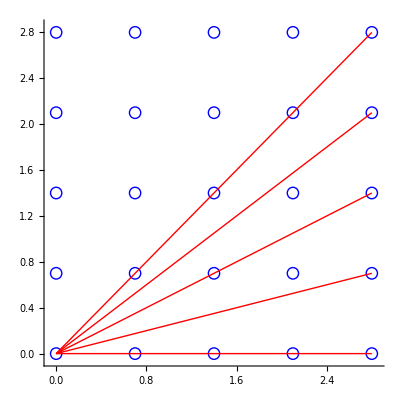

```mathematica
num=5;
a=0.7;
r[i_,j_] :=Graphics[{Red,Line[{a{Mod[i-1,num], Floor[(i-1)/num]},a{Mod[j-1,num],Floor[(j-1)/num]}}]}];
Show[Table[Graphics[{Blue,Circle[a{Mod[i-1,num],Floor[(i-1)/num]},0.05]}],{i,Range[num^2]}],Table[r[1,j],{j,{5,10,15,20,25}}],Axes->True]
```

```mathematica
r[i_,j_] :=a{Mod[j-1,num]-Mod[i-1,num],Floor[(j-1)/num]-Floor[(i-1)/num]};
```

```mathematica
r[1,15]
```

{2.8,1.4}

```mathematica
υ = Table[x^2+y^2,{x,{-1,0,1}},{y,{-1,0,1}}]
```

{{2,1,2},{1,0,1},{2,1,2}}

```mathematica
{1,0,1}.υ
```

{4,2,4}